# Textually Describing Wolfram Language Expressions

Renan Germano

Mackenzie Presbyterian University

The objective of the present project is to create a function to textually describe Wolfram Language expressions. This is done by developing an algorithm that is capable of better describing the input, based on its symbolic structure, where the output is a human readable String. Thinking about accessibility for visually impaired, this text could be used as an automatically generated alternative description for graphics and related content.

## Wolfram Community Post (material for blog post)

## Complete project work

### Manipulating Wolfram Language symbols

```mathematica
WolframLanguageData["List", "Properties"]
```

{attributes,character count,common option values,date introduced,date last modified,dates modified,documentation basic examples,documentation example counts,documentation example inputs,documentation example text,entity classes,eponymous people,equal-precedence symbols,external links,frequencies of usage,full version introduced,full version last modified,full versions modified,functionality areas,symbol background,keyboard shortcuts,link trails,memberships,name,option names,options,plaintext usage,precedence ranks,ranks of usage,related entities,related guide pages,related symbols,relationship community graph,relationship graph,short notations,subject classifications,symbols linking to,symbols using as attribute,symbols using as option,text strings,timeline,timeline events,translations,typeset usage,URL,version introduced,version last modified,versions modified,Wolfram documentation link}

```mathematica
?WolframLanguageData
```

```mathematica
wlSymbols=WolframLanguageData[];
```

```mathematica
wlSymbols//Length
```

5605

```mathematica
wlEntityProperties=WolframLanguageData["Properties"]
```

{attributes,character count,common option values,date introduced,date last modified,dates modified,documentation basic examples,documentation example counts,documentation example inputs,documentation example text,entity classes,eponymous people,equal-precedence symbols,external links,frequencies of usage,full version introduced,full version last modified,full versions modified,functionality areas,symbol background,keyboard shortcuts,link trails,memberships,name,option names,options,plaintext usage,precedence ranks,ranks of usage,related entities,related guide pages,related symbols,relationship community graph,relationship graph,short notations,subject classifications,symbols linking to,symbols using as attribute,symbols using as option,text strings,timeline,timeline events,translations,typeset usage,URL,version introduced,version last modified,versions modified,Wolfram documentation link}

```mathematica
functionalityAreasOfAllWLSymbols=MapThread[{#1,#2}&,{wlSymbols,EntityValue[wlSymbols,EntityProperty["WolframLanguageSymbol","FunctionalityAreas"]]}];
```

```mathematica
AllPropertiesForSymbol[symbol_Symbol]:=EntityValue[WolframLanguageData@ToString@symbol,wlEntityProperties]
```

```mathematica
RelationshipGraphs[symbol_Symbol]:=EntityValue[WolframLanguageData@ToString@symbol,{EntityProperty["WolframLanguageSymbol","RelationshipGraph"],EntityProperty["WolframLanguageSymbol","RelationshipCommunityGraph"]}]
```

### Already build-in functions to describe Wolfram Language expressions

```mathematica
redSphere=Graphics3D[{Red,Sphere[]}]
```

-Graphics3D-

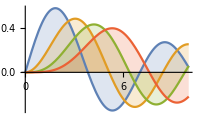

```mathematica
complexGraph=Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

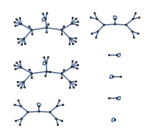

```mathematica
someGraphs=GraphPlot[Table[i->Mod[i^2,102],{i,0,102}]]
```

#### SpokenString

```mathematica
?SpokenString
SpokenString@redSphere
SpokenString@complexGraph
SpokenString@someGraphs
```

a three-dimensional graphic consisting of a sphere

a graphic consisting of 11 polygons, a line connecting 574 points, a line connecting 541 points, a line connecting 556 points and a line connecting 610 points

a graphic consisting of 103 arrows and 103 disks

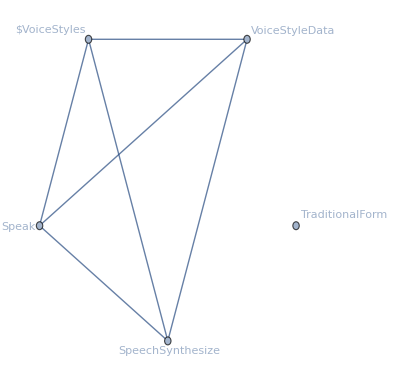
{-Graphics-,-Graphics-}

```mathematica
RelationshipGraphs@SpokenString
```

#### TextString

```mathematica
?TextString
TextString@redSphere
TextString@complexGraph
TextString@someGraphs
```

Graphics3D[{RGBColor[1, 0, 0], Sphere[{0, 0, 0}]}]

Graphics[…]

Graphics[…]

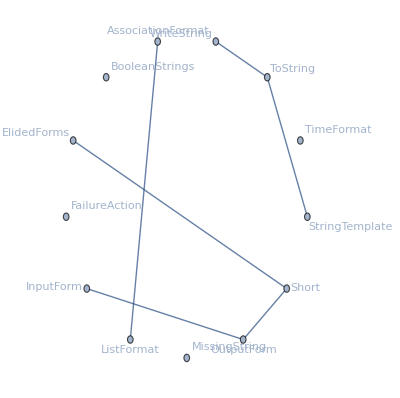
{-Graphics-,-Graphics-}

```mathematica
RelationshipGraphs@TextString
```

#### ToString

```mathematica
?ToString
ToString@redSphere
ToString@complexGraph
ToString@someGraphs
```

-Graphics3D-

-Graphics-

-Graphics-

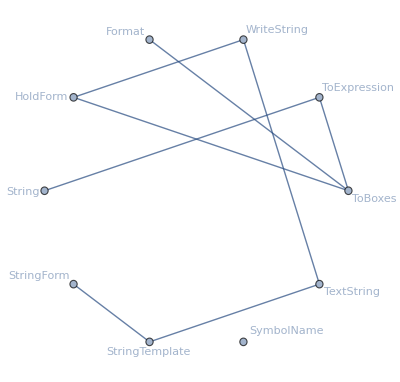
{-Graphics-,-Graphics-}

```mathematica
RelationshipGraphs@ToString
```

### Describing Colors

#### Named Colors

```mathematica
redNamedColorWLEntity=WolframLanguageData["Red"]
```

Red

```mathematica
entityPropertyValuesForRedColor={#,EntityValue[redNamedColorWLEntity, #]}&/@wlEntityProperties;
```

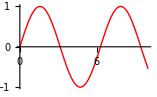
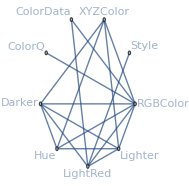
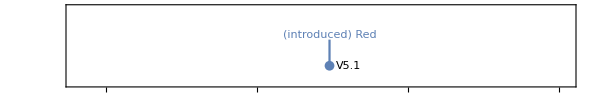
attributes | {Protected}
character count | 3
date introduced | Day: Mon 25 Oct 2004
documentation basic examples | {{Graphics[{Red,Disk[]}],-Graphics-,Plot[Sin[x],{x,0,10},PlotStyle→Red],-Graphics-,Graphics3D[{Red,Sphere[]}],-Graphics3D-}}
documentation example counts | {BasicExamples→1,Scope→0,GeneralizationsExtensions→0,Options→0,Applications→0,PropertiesRelations→0,PossibleIssues→0,InteractiveExamples→0,NeatExamples→0}
documentation example inputs | {BasicExamples→{{Graphics[{Red,Disk[]}],Plot[Sin[x],{x,0,10},PlotStyle→Red],Graphics3D[{Red,Sphere[]}]}},Scope→{},GeneralizationsExtensions→{},Options→{},Applications→{},PropertiesRelations→{},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{}}
documentation example text | {BasicExamples→{{}},Scope→{},GeneralizationsExtensions→{},Options→{},Applications→{},PropertiesRelations→{},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{}}
entity classes | {Wolfram Language autoevaluating symbols}
eponymous people | {}
external links | {}
frequencies of usage | {All→0.000434382,StackExchange→0.00233259,TypicalProductionCode→0.0010278,WolframAlphaCodebase→0.0000142108,WolframDemonstrations→0.00218411,WolframDocumentation→0.00162619}
full version introduced | 5.1
functionality areas | {ColorSymbols}
symbol background | Red is a symbol that represents the color red in graphics or style specifications. Color specifications in the Wolfram Language can appear explicitly inside a Graphics or Graphics3D expression (e.g. Graphics[{Red,Disk[]}]), in which case they affect all subsequent expressions until another specification overrides them. They can also be used as part of an option specification, either singly (e.g. Plot[Sin[x],{x,0,2Pi},PlotStyle->Red]) or as part of a Directive compound expression (e.g. Plot[Cos[x],{x,0,2Pi},PlotStyle->Directive[Thick,Red]]). Finally, they can appear inside Style wrappers that affect the appearance of text, equations, and notebook cells (e.g. Style[hello,Red]).
Red is a color located at one of the corners of the RGB color cube and evaluates to RGBColor[1,0,0].
Named symbols for other colors include Green, Blue, Black, White, Gray, Cyan, Magenta, Yellow, Brown, Orange, Pink, and Purple, as well as their LightRed etc. variants. Arbitrary colors can be input using Hue, RGBColor, CMYKColor, LABColor, LUVColor, or XYZColor. Colors can be modified using Lighter, Darker, and Blend. Colors may be converted between different systems using ColorConvert. The appearance of colors appearing in Graphics3D objects may be controlled using Glow, Specularity, and Lighting. The transparency of colored graphics objectives can be specified using Opacity. ColorData can be used to give a function that generates colors in a named color scheme.
link trails | {{guide/WolframRoot,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/GraphicsOptionsAndStyling,guide/Colors,ref/Red},{guide/WolframRoot,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ImageProcessing,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/ImageProcessing,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ChartingAndInformationVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ChartingAndInformationVisualization,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Finance,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/ActuarialComputation,guide/Finance,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ActuarialComputation,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/DateAndTime,guide/DateAndTimeVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/EarthSciencesDataAndComputation,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Finance,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Geodesy,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/LifeSciencesAndMedicineDataAndComputation,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/PeopleAndHistory,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/ProbabilityAndStatistics,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/DescriptiveStatistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Statistics,guide/DescriptiveStatistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/TimeSeries,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/TimeSeries,guide/DateAndTimeVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/TimeSeries,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red}}
memberships | {Wolfram Language autoevaluating symbols}
name | Red
option names | {}
options | {}
plaintext usage | Red represents the color red in graphics or style specifications.
ranks of usage | {All→91,StackExchange→41,TypicalProductionCode→87,WolframAlphaCodebase→398,WolframDemonstrations→48,WolframDocumentation→54}
related entities | {red}
related guide pages | {Colorspaclet:guide/Colors,Symbolic Graphics Languagepaclet:guide/SymbolicGraphicsLanguage,Graphics Options & Stylingpaclet:guide/GraphicsOptionsAndStyling,Graphics Annotation & Appearancepaclet:guide/GraphicsAnnotationAndAppearance,Graphics Directivespaclet:guide/GraphicsDirectives,Maps & Cartographypaclet:guide/MapsAndCartography,Color Processingpaclet:guide/ColorProcessing,Notebook Formatting & Stylingpaclet:guide/NotebookFormattingAndStyling,Chart Styling & Layoutpaclet:guide/ChartLayoutAndStyling,Graph Visualizationpaclet:guide/GraphVisualization,Text Stylingpaclet:guide/TextStyling,GeoGraphics Languagepaclet:guide/GeoGraphicsLanguage,Graph Styling, Labeling, and Layoutpaclet:guide/GraphStylingAndLabeling,Maps & Cartographypaclet:guide/MapsAndGeographicData}
related symbols | {LightRed,ColorData,Lighter,Darker,Hue,RGBColor,Style}
relationship community graph | -Graphics-
relationship graph | -Graphics-
symbols linking to | {ColorQ,Hue,LightRed,RGBColor,XYZColor}
symbols using as attribute | {}
symbols using as option | {}
text strings | {Red represents the color red in graphics or style specifications.,Red is equivalent to RGBColor[1,0,0].,Red is a symbol that represents the color red in graphics or style specifications. Color specifications in the Wolfram Language can appear explicitly inside a Graphics or Graphics3D expression (e.g. Graphics[{Red,Disk[]}]), in which case they affect all subsequent expressions until another specification overrides them. They can also be used as part of an option specification, either singly (e.g. Plot[Sin[x],{x,0,2Pi},PlotStyle->Red]) or as part of a Directive compound expression (e.g. Plot[Cos[x],{x,0,2Pi},PlotStyle->Directive[Thick,Red]]). Finally, they can appear inside Style wrappers that affect the appearance of text, equations, and notebook cells (e.g. Style["hello",Red]).,Red is a color located at one of the corners of the RGB color cube and evaluates to RGBColor[1,0,0].,Named symbols for other colors include Green, Blue, Black, White, Gray, Cyan, Magenta, Yellow, Brown, Orange, Pink, and Purple, as well as their LightRed etc. variants. Arbitrary colors can be input using Hue, RGBColor, CMYKColor, LABColor, LUVColor, or XYZColor. Colors can be modified using Lighter, Darker, and Blend. Colors may be converted between different systems using ColorConvert. The appearance of colors appearing in Graphics3D objects may be controlled using Glow, Specularity, and Lighting. The transparency of colored graphics objectives can be specified using Opacity. ColorData can be used to give a function that generates colors in a named color scheme.}
timeline | -Graphics-
timeline events | Day: Mon 25 Oct 2004Red
translations | {Simplified Chinese→红色,Traditional Chinese→紅色,French→rouge,German→rot,Modern Greek→κόκκινο,Japanese→赤,Korean→빨강,Lithuanian→raudonas,Polish→czerwony,Portuguese→vermelho,Russian→красный,Spanish→rojo,Ukrainian→червоний,Vietnamese→đỏ}
typeset usage | Red represents the color red in graphics or style specifications. 
URL | http://reference.wolfram.com/language/ref/Red.html
version introduced | 5.1
Wolfram documentation link | Redpaclet:ref/Red

```mathematica
Grid[Select[entityPropertyValuesForRedColor, Not@MissingQ@Last@#&], Frame->All]
```

```mathematica
colorSymbols=Select[functionalityAreasOfAllWLSymbols, (Length@Last@#)==1&&((First@Last@#)=="ColorSymbols")&]⟦All,1⟧
```

{Black,Blend,Blue,Brown,CMYKColor,ChromaticityPlot,ChromaticityPlot3D,ColorBalance,ColorCombine,ColorConvert,ColorCoverage,ColorData,ColorDataFunction,ColorDetect,ColorDistance,ColorFunction,ColorFunctionScaling,ColorNegate,ColorProfileData,ColorQ,ColorQuantize,ColorReplace,ColorRules,ColorSeparate,ColorSetter,ColorSpace,ColorToneMapping,Colorize,ColorsNear,Cyan,Darker,Dithering,FindMatchingColor,Glow,Gray,GrayLevel,Green,Hue,ImageColorSpace,LABColor,LCHColor,LUVColor,LightBlue,LightBrown,LightCyan,LightGray,LightGreen,LightMagenta,LightOrange,LightPink,LightPurple,LightRed,LightYellow,Lighter,Magenta,MaxColorDistance,MinColorDistance,Orange,Pink,Purple,RGBColor,RandomColor,Red,StreamColorFunction,StreamColorFunctionScaling,VectorColorFunction,VectorColorFunctionScaling,White,WhitePoint,XYZColor,Yellow}

```mathematica
namedColors= Select[colorSymbols,ColorQ@RGBColor@#["Name"]&]
```

{Black,Blue,Brown,Cyan,Gray,Green,LightBlue,LightCyan,LightGreen,LightPink,LightYellow,Magenta,Orange,Pink,Purple,Red,White,Yellow}

```mathematica
Grid[{#, RGBColor@#@"Name", #@"Name", #@"Translations"}&/@namedColors, Frame->All]
```

```mathematica
namedColorsRGB=Association[RGBColor@#@"Name"->#&/@namedColors]
```

<|RGBColor[0., 0., 0.]→Black,RGBColor[0., 0., 1.]→Blue,RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412]→Brown,RGBColor[0., 1., 1.]→Cyan,RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]→Gray,RGBColor[0., 0.5019607843137255, 0.]→Green,RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726]→LightBlue,RGBColor[0.87843137254902, 1., 1.]→LightCyan,RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411]→LightGreen,RGBColor[1., 0.7137254901960784, 0.7568627450980392]→LightPink,RGBColor[1., 1., 0.87843137254902]→LightYellow,RGBColor[1., 0., 1.]→Magenta,RGBColor[1., 0.6470588235294118, 0.]→Orange,RGBColor[1., 0.7529411764705882, 0.796078431372549]→Pink,RGBColor[0.5019607843137255, 0., 0.5019607843137255]→Purple,RGBColor[1., 0., 0.]→Red,RGBColor[1., 1., 1.]→White,RGBColor[1., 1., 0.]→Yellow|>

```mathematica
MyColorDistance[color1_RGBColor,color2_RGBColor]:=N[Mean[MapThread[Abs[#1-#2]&,{List@@color1,List@@color2}]]]
MyColorDistance[Red,Red]
MyColorDistance[Red,Green]
MyColorDistance[Red,Blue]
MyColorDistance[Red,Pink]
MyColorDistance[Red,Black]
```

0.

0.666667

0.666667

0.333333

MyColorDistance[RGBColor[1, 0, 0],GrayLevel[0]]

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
nearestColor = Nearest[Keys@namedColorsRGB,randomColor,1]//First
namedColorsRGB[nearestColor]["Name"]
Association[namedColorsRGB[nearestColor]["Translations"]][Entity["Language","Portuguese"]]
```

RGBColor[0.32791526849313435, 0.4964549822940518, 0.007826250271401713]

RGBColor[0., 0.5019607843137255, 0.]

Green

verde

```mathematica
Clear[Description]
```

```mathematica
Description[color_RGBColor]:=Description[color]=namedColorsRGB[First@Nearest[Keys@namedColorsRGB,color,1]]@"Name"
```

```mathematica
SetAttributes[Description,Listable]
```

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
Description[randomColor]
```

RGBColor[0.09016625083697405, 0.7331979635438117, 0.993214193617989]

LightBlue

```mathematica
tests={#, Style[Description@#,#]}&/@RGBColor/@RandomReal[1,{100,3}];
```

```mathematica
Grid[#,Frame->All,Alignment->Left]&/@ArrayReshape[tests,{5,20,2}]
```

{RGBColor[{0.8844645097370236, 0.15371387611368093, 0.08636159643020758}] | Red
RGBColor[{0.9647245760891741, 0.3467506020558946, 0.3550011312463166}] | Brown
RGBColor[{0.7845641395288916, 0.9224776636284278, 0.23946108133284594}] | Yellow
RGBColor[{0.7644545378213938, 0.4524653058478012, 0.9627680584003422}] | Purple
RGBColor[{0.8896820635381595, 0.8589680771091972, 0.5506153945217334}] | LightYellow
RGBColor[{0.011014049340050125, 0.9288541812273803, 0.4501725806935579}] | LightGreen
RGBColor[{0.7316669318304507, 0.1880266310782519, 0.36779098116806286}] | Brown
RGBColor[{0.9249393534503008, 0.2080531664534233, 0.7743270854412696}] | Magenta
RGBColor[{0.5178347740509959, 0.9950228118422042, 0.7956008838788802}] | LightGreen
RGBColor[{0.8638972661717459, 0.3765980482811808, 0.9081654580822598}] | Purple
RGBColor[{0.844419319683273, 0.7736848502626545, 0.5678495884098373}] | LightYellow
RGBColor[{0.37583088564839673, 0.4545428499796462, 0.5370252601023993}] | Gray
RGBColor[{0.4043662463478406, 0.2230587047550603, 0.40624998168224047}] | Purple
RGBColor[{0.20437419999993756, 0.35412471265799494, 0.41406139900231254}] | Gray
RGBColor[{0.10477474355212069, 0.8726190114345234, 0.05335483352360626}] | Green
RGBColor[{0.9910232897057194, 0.6114438961336219, 0.6386074847553191}] | LightPink
RGBColor[{0.7291096056242083, 0.644132966397482, 0.030438550492523753}] | Orange
RGBColor[{0.10375185493197114, 0.8185528139393747, 0.22774302194048346}] | LightGreen
RGBColor[{0.935912822663052, 0.40204955688283905, 0.24264566700244217}] | Brown
RGBColor[{0.7800544567215193, 0.7373870240359899, 0.46553447556809413}] | LightYellow,RGBColor[{0.30667534993952184, 0.7408428647536442, 0.6913203553140477}] | LightBlue
RGBColor[{0.3978915495366573, 0.3174857122838799, 0.034978378752248185}] | Gray
RGBColor[{0.7277974840280546, 0.7800779295702058, 0.7803461178999349}] | LightBlue
RGBColor[{0.5612982814002196, 0.9657245037108324, 0.49512325131607593}] | LightGreen
RGBColor[{0.7184771439379725, 0.9711241892368632, 0.34919259027637106}] | LightGreen
RGBColor[{0.3882570871072719, 0.03907567366724152, 0.5609604738676774}] | Purple
RGBColor[{0.27438238375167834, 0.8965372982710695, 0.428792076038778}] | LightGreen
RGBColor[{0.7345235558056227, 0.36461625733585157, 0.6614754804085177}] | Purple
RGBColor[{0.12609057546352642, 0.4033449015544701, 0.7418263727162968}] | Gray
RGBColor[{0.6372672591435493, 0.705372450770779, 0.5763656273143103}] | Gray
RGBColor[{0.18132208199659772, 0.5968515534365535, 0.0007884042250807521}] | Green
RGBColor[{0.7212661945196535, 0.34836835617083084, 0.8264055350596995}] | Purple
RGBColor[{0.48656839337937763, 0.5117282020178104, 0.9285855828637883}] | Purple
RGBColor[{0.6740862743239757, 0.04252352178008989, 0.8379395160386349}] | Magenta
RGBColor[{0.11516390112798902, 0.9807641695569262, 0.8371887721379885}] | Cyan
RGBColor[{0.5217587677225544, 0.9399822052707618, 0.37209801493702166}] | LightGreen
RGBColor[{0.8306425300530027, 0.9266634271265473, 0.8657312913606883}] | LightCyan
RGBColor[{0.4190990038203102, 0.45275532914356864, 0.6365830335143416}] | Gray
RGBColor[{0.7489338153738216, 0.3966044530142032, 0.8724712336679223}] | Purple
RGBColor[{0.7562649975977134, 0.8993816140643478, 0.38007261274823523}] | LightGreen,RGBColor[{0.05700695224314267, 0.037483092803455964, 0.44617783192256977}] | Purple
RGBColor[{0.2643085197558974, 0.8605080771542835, 0.680535117625896}] | LightGreen
RGBColor[{0.7165099588232322, 0.6237206682399772, 0.17008206670761128}] | Orange
RGBColor[{0.6145555487063059, 0.9453344633076104, 0.008557787962381935}] | Yellow
RGBColor[{0.40794755108540204, 0.10706693365204312, 0.4361407729174096}] | Purple
RGBColor[{0.9059546211098441, 0.13034936771721317, 0.8288262460782607}] | Magenta
RGBColor[{0.6294749703574136, 0.5529172010797676, 0.35578643147136635}] | Gray
RGBColor[{0.7754321353183709, 0.03639352605362878, 0.454578662358899}] | Purple
RGBColor[{0.3191892338454554, 0.819342346148729, 0.22168047489435327}] | LightGreen
RGBColor[{0.16261167910507335, 0.2274527530052608, 0.6212381221153827}] | Purple
RGBColor[{0.09060140797229721, 0.09208139687570993, 0.9448296176885811}] | Blue
RGBColor[{0.15373090519586752, 0.4078879956540955, 0.7876934624549614}] | Purple
RGBColor[{0.49611056672197074, 0.3830358890266916, 0.7190911266460225}] | Purple
RGBColor[{0.8805799392092344, 0.40986928263124267, 0.8791511920949033}] | Purple
RGBColor[{0.4761611144859146, 0.11907397702903988, 0.6337585942571544}] | Purple
RGBColor[{0.49941185694156154, 0.26402432785593954, 0.4260811171140353}] | Purple
RGBColor[{0.8711299791124678, 0.7031145044489051, 0.9660925250460055}] | Pink
RGBColor[{0.2623121228445311, 0.1657259943182834, 0.08777080866164777}] | Black
RGBColor[{0.5132308100048208, 0.4954106416246742, 0.4559560453529594}] | Gray
RGBColor[{0.48683529298779993, 0.434134146380579, 0.2609294517408076}] | Gray,RGBColor[{0.7809824940910832, 0.42196201679475553, 0.616048540739736}] | LightPink
RGBColor[{0.20766719593207306, 0.07988713623407628, 0.6832822435400336}] | Purple
RGBColor[{0.7839500119192122, 0.41974202875712807, 0.859696022270291}] | Purple
RGBColor[{0.6749103990582181, 0.5413414955123752, 0.6841753000520348}] | Gray
RGBColor[{0.332053303530778, 0.29067422455813574, 0.352190668721976}] | Gray
RGBColor[{0.308738339593005, 0.860684387464917, 0.12746720712051407}] | LightGreen
RGBColor[{0.5352822686079881, 0.43257610320368767, 0.2490748532081033}] | Gray
RGBColor[{0.8997990062996704, 0.8841237341556785, 0.5692032136091647}] | LightYellow
RGBColor[{0.8580553370698385, 0.21678905512758928, 0.5872351915822489}] | Purple
RGBColor[{0.276754844064075, 0.9996111255333615, 0.037993793376354335}] | LightGreen
RGBColor[{0.6250519741338343, 0.5906653146355225, 0.5602814662154543}] | Gray
RGBColor[{0.946978996752194, 0.46223521348099994, 0.9135997342381239}] | Purple
RGBColor[{0.6246088987403531, 0.25930702232591196, 0.8724416721746653}] | Purple
RGBColor[{0.9960334686309267, 0.13277828636588263, 0.527997784512229}] | Brown
RGBColor[{0.6451749655811749, 0.6123034521272857, 0.12733841060938156}] | Orange
RGBColor[{0.938208106693361, 0.2999897044261213, 0.2663601479234303}] | Brown
RGBColor[{0.8436689307439655, 0.359815825675881, 0.19128380401398237}] | Brown
RGBColor[{0.9476842328147068, 0.2054777204220699, 0.588791550821725}] | Purple
RGBColor[{0.3247589760242333, 0.5255801528404058, 0.25989646285362733}] | Green
RGBColor[{0.9624502169661007, 0.47787600156136945, 0.13029277543501694}] | Orange,RGBColor[{0.019112855914706683, 0.7962891288703811, 0.3757245647441094}] | LightGreen
RGBColor[{0.7856690536746274, 0.006504202271225612, 0.06384890230957363}] | Red
RGBColor[{0.2904552548465713, 0.13572623487354063, 0.9696575442845774}] | Blue
RGBColor[{0.7807354215105389, 0.7988381605789117, 0.05174917399836931}] | Yellow
RGBColor[{0.9718629653026318, 0.48182537761458466, 0.4357370387446391}] | Brown
RGBColor[{0.4011780127727904, 0.962934865744792, 0.34267368362893835}] | LightGreen
RGBColor[{0.14772091889692351, 0.3299550027488807, 0.8144379385853606}] | Purple
RGBColor[{0.1115540457985309, 0.892391613866375, 0.7391236816237745}] | Cyan
RGBColor[{0.2631193877034492, 0.46946681455663963, 0.8155196635555793}] | Gray
RGBColor[{0.43594276531800125, 0.6337145101205324, 0.9541694691404092}] | LightBlue
RGBColor[{0.6730973336448016, 0.29906018651138044, 0.3327377132099114}] | Brown
RGBColor[{0.8797153604424279, 0.7991498205035255, 0.43885543276539996}] | LightYellow
RGBColor[{0.4414612468373773, 0.023139215009285063, 0.8831143197328546}] | Blue
RGBColor[{0.23554654444452772, 0.39345790724806307, 0.16751850011276326}] | Green
RGBColor[{0.1709125455742273, 0.13995314028317796, 0.3110108724474223}] | Black
RGBColor[{0.10215306142074687, 0.8786176109191173, 0.5396958043338422}] | LightGreen
RGBColor[{0.9511077183231478, 0.4554299818719456, 0.11963638355302342}] | Orange
RGBColor[{0.059435879862692165, 0.2478860097606912, 0.4127381815198561}] | Black
RGBColor[{0.8685229865381641, 0.8329490363818071, 0.13936988254910165}] | Yellow
RGBColor[{0.3078750342923273, 0.22274909382534314, 0.3148555791768579}] | Gray}

```mathematica
$Language
```

English

```mathematica
Clear[TranslatedDescription]
```

```mathematica
TranslatedDescription[color_RGBColor]:=TranslatedDescription[color]=Description[color]
TranslatedDescription[color_RGBColor,language_String]:=TranslatedDescription[color,language]=Association[namedColorsRGB[First@Nearest[Keys@namedColorsRGB,color,1]]["Translations"]][Entity["Language",language]]
```

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
TranslatedDescription[randomColor,"Japanese"]
```

RGBColor[0.9155897242155773, 0.5090670770077599, 0.9419598631904365]

紫色

```mathematica
tests2={#, Style[Description@#,#],Style[TranslatedDescription[#,"Spanish"],#]}&/@RGBColor/@RandomReal[1,{100,3}];
```

```mathematica
Grid[#,Frame->All,Alignment->Left]&/@ArrayReshape[tests2,{5,20,3}]
```

{RGBColor[{0.3627923631536394, 0.6700676074489256, 0.24370761425527965}] | Green | verde
RGBColor[{0.25197175319343246, 0.5523250784626585, 0.04437002126412026}] | Green | verde
RGBColor[{0.9999422564996538, 0.3315555815906719, 0.3614261881231009}] | Brown | marrón
RGBColor[{0.6760737783172028, 0.9719467269269473, 0.565954084445146}] | LightGreen | verde claro
RGBColor[{0.5456945107514106, 0.515110636680685, 0.30566080927846584}] | Gray | gris
RGBColor[{0.3599628272024382, 0.7685760529444299, 0.6136350660966825}] | LightGreen | verde claro
RGBColor[{0.11939414834187434, 0.550271585526287, 0.8227573949780616}] | LightBlue | azul claro
RGBColor[{0.39911166805852805, 0.9048405043662759, 0.014694975472994587}] | LightGreen | verde claro
RGBColor[{0.3201493929935366, 0.8601819330324187, 0.4930651040084735}] | LightGreen | verde claro
RGBColor[{0.7856198924240909, 0.47211297073193226, 0.04620645888667152}] | Orange | naranja
RGBColor[{0.888811635883904, 0.4204842093029708, 0.9770595119289869}] | Magenta | magenta
RGBColor[{0.07112833428934229, 0.0030461924480484903, 0.5354076272299284}] | Purple | púrpura
RGBColor[{0.32516426007039234, 0.2723049650656397, 0.15336440780022254}] | Gray | gris
RGBColor[{0.7780722312438502, 0.03169840533770163, 0.7505274601219387}] | Magenta | magenta
RGBColor[{0.9513429523275865, 0.7174281048917253, 0.022666960342985876}] | Orange | naranja
RGBColor[{0.7999148238586657, 0.9775009005886401, 0.8380351934204902}] | LightYellow | amarillo claro
RGBColor[{0.27696624590424457, 0.7307448556708658, 0.8529244118142227}] | LightBlue | azul claro
RGBColor[{0.39600775184124637, 0.7389652592865184, 0.26396245040627964}] | LightGreen | verde claro
RGBColor[{0.3982076801865495, 0.6555704337529253, 0.2648147249320807}] | Green | verde
RGBColor[{0.6662986862044804, 0.7999816011700616, 0.6601056684734803}] | LightYellow | amarillo claro,RGBColor[{0.1709446444874596, 0.696240928522389, 0.6118995682909458}] | Cyan | cian
RGBColor[{0.10251380304907265, 0.2772727721999051, 0.8147407884334235}] | Purple | púrpura
RGBColor[{0.3698902541332929, 0.21703579111755888, 0.6591733659074517}] | Purple | púrpura
RGBColor[{0.6659750681502481, 0.9853525891735426, 0.8202298695855192}] | LightGreen | verde claro
RGBColor[{0.32570394928294966, 0.09370081529164209, 0.8343757950105182}] | Blue | azul
RGBColor[{0.7542740821337834, 0.485822646351896, 0.3996831282782516}] | LightPink | rosa claro
RGBColor[{0.1629975314588794, 0.06880540435167593, 0.4445543179603224}] | Purple | púrpura
RGBColor[{0.6557040626585438, 0.3590705444496878, 0.4473155580515209}] | LightPink | rosa claro
RGBColor[{0.14488807271772952, 0.23574681362784844, 0.8105327636450546}] | Blue | azul
RGBColor[{0.024626406428259084, 0.38337318973285783, 0.7583736177996674}] | Purple | púrpura
RGBColor[{0.8164552502106011, 0.21505375993323006, 0.6271627044398767}] | Purple | púrpura
RGBColor[{0.9399077016589099, 0.6978375104727599, 0.07008797483859275}] | Orange | naranja
RGBColor[{0.5381643998608039, 0.05355007920290955, 0.04315098117934846}] | Brown | marrón
RGBColor[{0.2153774431075821, 0.3192902514277767, 0.9655587283146583}] | Blue | azul
RGBColor[{0.1855355591377097, 0.04515376593866405, 0.3749154852900669}] | Purple | púrpura
RGBColor[{0.9241542387126924, 0.5377079615966656, 0.577240323404125}] | LightPink | rosa claro
RGBColor[{0.15125763092866995, 0.6269621801290677, 0.054725616250126397}] | Green | verde
RGBColor[{0.7943022506730717, 0.9152070493764748, 0.9093356361338798}] | LightCyan | cian claro
RGBColor[{0.5187592755169463, 0.8081666806280257, 0.6120460241811359}] | LightGreen | verde claro
RGBColor[{0.2665318653763975, 0.5945577322039735, 0.6874917294964318}] | LightBlue | azul claro,RGBColor[{0.5536771311435695, 0.8968920050481259, 0.9994909170732498}] | LightBlue | azul claro
RGBColor[{0.6007236123939588, 0.15964165356136317, 0.8727354871409454}] | Magenta | magenta
RGBColor[{0.933169822468497, 0.2572719407349371, 0.2955655672475588}] | Brown | marrón
RGBColor[{0.829340044550821, 0.5192102170304791, 0.9181755083317085}] | Purple | púrpura
RGBColor[{0.4373345451071391, 0.21140121088292907, 0.11424322782623508}] | Brown | marrón
RGBColor[{0.04058708173847969, 0.6977278991168749, 0.42828407375539723}] | LightGreen | verde claro
RGBColor[{0.7790921948841647, 0.5682964628634037, 0.7205323015846086}] | LightPink | rosa claro
RGBColor[{0.4529133769540896, 0.7676073850579612, 0.8976193828089725}] | LightBlue | azul claro
RGBColor[{0.1922776595903899, 0.5947681021250284, 0.5559094031245402}] | Gray | gris
RGBColor[{0.6482641113170375, 0.39327269882349514, 0.2897924336601343}] | Brown | marrón
RGBColor[{0.660460941480546, 0.9396410326758409, 0.03295609126638577}] | Yellow | amarillo
RGBColor[{0.2805687016350831, 0.03501387196586725, 0.8794590216211728}] | Blue | azul
RGBColor[{0.002699814805857681, 0.7407444182765939, 0.27641944755282055}] | Green | verde
RGBColor[{0.41967208838513703, 0.768003961691315, 0.47773784308035916}] | LightGreen | verde claro
RGBColor[{0.4218849283174211, 0.020743268149578276, 0.7846945896877526}] | Blue | azul
RGBColor[{0.3651030011716081, 0.728943892900511, 0.09330910850244423}] | Green | verde
RGBColor[{0.6071396238483284, 0.6666235040047288, 0.6313503500831297}] | Gray | gris
RGBColor[{0.04008439256125795, 0.7044807716138592, 0.6832948460689896}] | Cyan | cian
RGBColor[{0.7460376834345042, 0.6128497562755799, 0.936127180528554}] | Pink | rosa
RGBColor[{0.9439879598984464, 0.4053735251779709, 0.9505453910155639}] | Magenta | magenta,RGBColor[{0.22484306228618478, 0.3869403453039437, 0.9498157219938261}] | Purple | púrpura
RGBColor[{0.3977530714572859, 0.39095714874443366, 0.6060257564833513}] | Gray | gris
RGBColor[{0.5986428599057025, 0.7893442934164312, 0.24233179486437728}] | LightGreen | verde claro
RGBColor[{0.55157278135049, 0.535002296472959, 0.013216071647603522}] | Green | verde
RGBColor[{0.5002717904736937, 0.40128324051579467, 0.11612023234877755}] | Gray | gris
RGBColor[{0.8780563613379249, 0.8854958213046666, 0.7740531140072}] | LightYellow | amarillo claro
RGBColor[{0.11319996370888386, 0.7184906916454454, 0.3755510013385035}] | LightGreen | verde claro
RGBColor[{0.6204318838424203, 0.46017277401602685, 0.26009513796255335}] | Gray | gris
RGBColor[{0.6139866465519133, 0.017250543809972596, 0.23150174975433546}] | Brown | marrón
RGBColor[{0.08084230932105951, 0.3290261558019447, 0.22441666919344105}] | Gray | gris
RGBColor[{0.9609403352632147, 0.6445409479794544, 0.5123690207716576}] | LightPink | rosa claro
RGBColor[{0.2949443842166213, 0.4339071020866625, 0.06264494797061859}] | Green | verde
RGBColor[{0.11313853871118273, 0.7440612635501003, 0.8506036338713907}] | LightBlue | azul claro
RGBColor[{0.3869956405280335, 0.2971994814627126, 0.15990776943136065}] | Gray | gris
RGBColor[{0.4405459058636829, 0.2973924170915103, 0.21816698739797924}] | Gray | gris
RGBColor[{0.3979942127364118, 0.34748643517705347, 0.42908690320258636}] | Gray | gris
RGBColor[{0.34405483555498306, 0.5601256862067645, 0.6527506324952028}] | Gray | gris
RGBColor[{0.14771241561096748, 0.14923772867302842, 0.544799380413844}] | Purple | púrpura
RGBColor[{0.3050815817371104, 0.06123227652796004, 0.7258701224305286}] | Blue | azul
RGBColor[{0.6010052193677775, 0.29003578725160417, 0.17210775549553547}] | Brown | marrón,RGBColor[{0.7617465015669134, 0.16625598579749923, 0.03172669801963579}] | Brown | marrón
RGBColor[{0.8373998163777019, 0.1928679056768441, 0.5545837759463474}] | Purple | púrpura
RGBColor[{0.7716360262912063, 0.4319200280053923, 0.7464681650190428}] | Purple | púrpura
RGBColor[{0.8758269625206287, 0.4702414636032297, 0.19750037232065143}] | Orange | naranja
RGBColor[{0.23413325681914232, 0.6271783737843328, 0.10339572039997136}] | Green | verde
RGBColor[{0.17952436203198685, 0.4826426503368748, 0.19542383685884812}] | Green | verde
RGBColor[{0.1903737318364327, 0.7508589688752478, 0.9915939009986174}] | LightBlue | azul claro
RGBColor[{0.2137440534163051, 0.3426424214416146, 0.5023063661007161}] | Gray | gris
RGBColor[{0.006421704331404543, 0.0957192078003255, 0.4416142479491483}] | Purple | púrpura
RGBColor[{0.5602784030991526, 0.4620618553738216, 0.06898733117633826}] | Orange | naranja
RGBColor[{0.5920456991080361, 0.8855513595666267, 0.3993625949624262}] | LightGreen | verde claro
RGBColor[{0.6191701829703513, 0.24188542877491792, 0.6828988618675471}] | Purple | púrpura
RGBColor[{0.9205444853464779, 0.3960806136513886, 0.7624448225911493}] | Purple | púrpura
RGBColor[{0.5615082104835545, 0.9677378264545677, 0.21230818372162386}] | LightGreen | verde claro
RGBColor[{0.4968576919597114, 0.27549372559803964, 0.4718681250209382}] | Purple | púrpura
RGBColor[{0.4595370639820353, 0.07795496343566066, 0.6199279478345683}] | Purple | púrpura
RGBColor[{0.40275818734017643, 0.05416262854296616, 0.48864015987152043}] | Purple | púrpura
RGBColor[{0.7104250490659039, 0.717475995303646, 0.35929133207348185}] | LightGreen | verde claro
RGBColor[{0.3899342526260603, 0.7887431407972076, 0.17793641186909515}] | Green | verde
RGBColor[{0.24870615087585746, 0.8155015601602773, 0.2983836217191307}] | LightGreen | verde claro}

#### ColorData

```mathematica
colors=Select[Flatten[ColorData[#,"ColorList"]&/@Flatten[ColorData/@ColorData[]]],!MissingQ[#]&]//Join//Sort;
```

```mathematica
colors//Length
colors[[;;10]]
```

2143

{GrayLevel[0.393668],GrayLevel[0.501961],GrayLevel[0.642527],GrayLevel[0.660639],GrayLevel[1],Hue[0, 0.33, 0.6],Hue[0, 0.33, 0.66],Hue[0, 0.5, 0.44],Hue[0, 0.5, 0.6],Hue[0, 0.5, 0.85]}

#### Entity Color

```mathematica
allColorEntities = EntityValue["Color", "Entities"];
```

```mathematica
allColorEntities//Length
```

10386

```mathematica
EntityValue["Color", "Properties"]
```

{analogous colors,brightness,CIE  L^*a^*b^*,CMYK,color split-complements,color tetrad,color triad,complementary color,complementary colors,entity classes,gray level,hexadecimal,HSB,HSI,HSL,HSV,hue,Hunter  Lab,intensity,lightness,L^*u^*v^*,monochromatic colors,name,flags with nearby colors,flags with nearby colors,nearest named brand colors,nearest named HTML colors,nearest Pantone colors,24-bit RGB,saturation,24-bit sRGB,Wolfram Language,xyY,XYZ}

```mathematica
nameAndColorEntities=EntityValue[EntityValue["Color", "Entities"],{EntityProperty["Color","Name"],EntityProperty["Color","RGBValue"]}]
```

{{HTML peach,color red:1. green:0.854902 blue:0.72549},{Colorado Yellow,color red:0.956863 green:0.858824 blue:0.517647},{Condor Yellow,color red:0.929412 green:0.92549 blue:0.654902},{Sahara,color red:0.929412 green:0.827451 blue:0.654902},{Ceylon Gold Metallic,color red:0.862745 green:0.752941 blue:0.454902},{Sienna Brown Metallic,color red:0.376471 green:0.196078 blue:0.137255},{Sierra Beige,color red:0.701961 green:0.639216 blue:0.396078},{Topaz Brown Metallic,color red:0.498039 green:0.239216 blue:0.137255},{Iberian Red,color red:0.733333 green:0.0196078 blue:0.0705882},{Ruby Red Metallic,color red:0.556863 green:0.137255 blue:0.160784},{Coral,color red:0.0313725 green:0.364706 blue:0.556863},{Malaga Red,color red:0.427451 green:0.0980392 blue:0.113725},{Inka (Orange),color red:0.92549 green:0.588235 blue:0.188235},{Verona Red (Light),color red:0.94902 green:0.27451 blue:0.243137},{Granite Metallic,color red:0.529412 green:0.133333 blue:0.156863},{Madeira,color red:0.439216 green:0.180392 blue:0.180392},{Phoenix Orange,color red:0.882353 green:0.541176 blue:0.137255},{Riviera Blue,color red:0.356863 green:0.470588 blue:0.568627},10350,{traffic sign purple (daytime),color red:0.368627 green:0.156863 blue:0.34902},{traffic sign red (daytime),color red:0.670588 green:0.196078 blue:0.14902},{traffic sign white (daytime),color red:1. green:1. blue:1.},{traffic sign yellow (daytime),color red:0.976471 green:0.815686 blue:0.313725},{traffic sign black (nighttime),color red:0. green:0. blue:0.},{traffic sign blue (nighttime),color red:0. green:0.364706 blue:0.643137},{traffic sign brown (nighttime),color red:0.427451 green:0.231373 blue:0.},{traffic sign fluorescent green (nighttime),color red:0. green:0.52549 blue:0.631373},{traffic sign fluorescent orange (nighttime),color red:0.690196 green:0.305882 blue:0.},{traffic sign fluorescent red (nighttime),color red:0.811765 green:0.141176 blue:0.},{traffic sign fluorescent yellow (nighttime),color red:0.627451 green:0.45098 blue:0.},{traffic sign fluorescent yellow green (nighttime),color red:0.458824 green:0.513725 blue:0.},{traffic sign green (nighttime),color red:0. green:0.380392 blue:0.458824},{traffic sign orange (nighttime),color red:0.74902 green:0.419608 blue:0.},{traffic sign purple (nighttime),color red:0. green:0. blue:1.},{traffic sign red (nighttime),color red:0.537255 green:0.168627 blue:0.},{traffic sign white (nighttime),color red:0.996078 green:1. blue:0.756863},{traffic sign yellow (nighttime),color red:0.643137 green:0.588235 blue:0.}}
 |  |  |  |

```mathematica
rgbColors = Association[RGBColor@Last@Last@Last@#->First@#&/@nameAndColorEntities]
```

<|RGBColor[{255, 218, 185}]→HTML peach puff,RGBColor[{244, 219, 132}]→Colorado Yellow,RGBColor[{237, 236, 167}]→Condor Yellow,RGBColor[{237, 211, 167}]→Sahara,RGBColor[{220, 192, 116}]→Ceylon Gold Metallic,RGBColor[{96, 50, 35}]→Sienna Brown Metallic,RGBColor[{179, 163, 101}]→Sierra Beige,RGBColor[{127, 61, 35}]→Topaz Brown Metallic,RGBColor[{187, 5, 18}]→Iberian Red,8615,RGBColor[{207, 36, 0}]→traffic sign fluorescent red (nighttime),RGBColor[{160, 115, 0}]→traffic sign fluorescent yellow (nighttime),RGBColor[{117, 131, 0}]→traffic sign fluorescent yellow green (nighttime),RGBColor[{0, 97, 117}]→traffic sign green (nighttime),RGBColor[{191, 107, 0}]→traffic sign orange (nighttime),RGBColor[{137, 43, 0}]→traffic sign red (nighttime),RGBColor[{254, 255, 193}]→traffic sign white (nighttime),RGBColor[{164, 150, 0}]→traffic sign yellow (nighttime)|>
 |  |  |  |

```mathematica
rgbColors=Association[#->rgbColors[#]&/@Join[rgbColors//Keys]]
```

<|RGBColor[{255, 218, 185}]→HTML peach puff,RGBColor[{244, 219, 132}]→Colorado Yellow,RGBColor[{237, 236, 167}]→Condor Yellow,RGBColor[{237, 211, 167}]→Sahara,RGBColor[{220, 192, 116}]→Ceylon Gold Metallic,RGBColor[{96, 50, 35}]→Sienna Brown Metallic,RGBColor[{179, 163, 101}]→Sierra Beige,RGBColor[{127, 61, 35}]→Topaz Brown Metallic,RGBColor[{187, 5, 18}]→Iberian Red,RGBColor[{142, 35, 41}]→Ruby Red Metallic,RGBColor[{8, 93, 142}]→Coral,RGBColor[{109, 25, 29}]→Malaga Red,RGBColor[{236, 150, 48}]→Inka (Orange),RGBColor[{242, 70, 62}]→Verona Red (Light),RGBColor[{135, 34, 40}]→Granite Metallic,RGBColor[{112, 46, 46}]→Madeira,RGBColor[{225, 138, 35}]→Phoenix Orange,RGBColor[{91, 120, 145}]→Riviera Blue,RGBColor[{186, 208, 214}]→Fjord Blue Metallic,8594,RGBColor[{32, 100, 72}]→traffic sign green (daytime),RGBColor[{0, 158, 223}]→traffic sign light blue (daytime),RGBColor[{103, 180, 68}]→traffic sign light green (daytime),RGBColor[{232, 136, 44}]→traffic sign orange (daytime),RGBColor[{94, 40, 89}]→traffic sign purple (daytime),RGBColor[{171, 50, 38}]→traffic sign red (daytime),RGBColor[{249, 208, 80}]→traffic sign yellow (daytime),RGBColor[{0, 93, 164}]→traffic sign blue (nighttime),RGBColor[{109, 59, 0}]→traffic sign brown (nighttime),RGBColor[{0, 134, 161}]→traffic sign fluorescent green (nighttime),RGBColor[{176, 78, 0}]→traffic sign fluorescent orange (nighttime),RGBColor[{207, 36, 0}]→traffic sign fluorescent red (nighttime),RGBColor[{160, 115, 0}]→traffic sign fluorescent yellow (nighttime),RGBColor[{117, 131, 0}]→traffic sign fluorescent yellow green (nighttime),RGBColor[{0, 97, 117}]→traffic sign green (nighttime),RGBColor[{191, 107, 0}]→traffic sign orange (nighttime),RGBColor[{137, 43, 0}]→traffic sign red (nighttime),RGBColor[{254, 255, 193}]→traffic sign white (nighttime),RGBColor[{164, 150, 0}]→traffic sign yellow (nighttime)|>
 |  |  |  |

```mathematica
Clear[Description2]
```

```mathematica
Description2[color_RGBColor]:=Description2[color]=rgbColors[First@Nearest[Keys@rgbColors,color,1]]
```

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
Description2[randomColor]
```

RGBColor[0.751695460169401, 0.5362712005214052, 0.9943670576474164]

traffic sign black (nighttime)

```mathematica
tests3={#, Style[Description@#,#]}&/@RGBColor/@RandomReal[1,{100,3}];
```

```mathematica
Grid[#,Frame->All,Alignment->Left]&/@ArrayReshape[tests3,{5,20,2}]
```

{RGBColor[{0.5845098539763065, 0.013996114120617964, 0.008965731558584489}] | traffic sign black (nighttime)
RGBColor[{0.5245985735329484, 0.15292378117946281, 0.6188841016800584}] | traffic sign black (nighttime)
RGBColor[{0.4271963084626904, 0.9097057120368814, 0.47392767396176727}] | traffic sign black (nighttime)
RGBColor[{0.4226959070581713, 0.653419688985245, 0.8369638921645741}] | traffic sign black (nighttime)
RGBColor[{0.7100614649528822, 0.1084927727331162, 0.010805527529188508}] | traffic sign black (nighttime)
RGBColor[{0.20994568736423225, 0.04204732262036193, 0.34392697564915586}] | traffic sign black (nighttime)
RGBColor[{0.8606697812146464, 0.7820159808554155, 0.7172038610484703}] | traffic sign black (nighttime)
RGBColor[{0.3114594228887346, 0.6942543008096671, 0.5254497733183099}] | traffic sign black (nighttime)
RGBColor[{0.027801032458370623, 0.8500549665632668, 0.38049262241152193}] | traffic sign black (nighttime)
RGBColor[{0.14809218597080953, 0.35373679692857385, 0.7393775063576036}] | traffic sign black (nighttime)
RGBColor[{0.489032917351246, 0.5189150836850291, 0.3735049798772665}] | traffic sign black (nighttime)
RGBColor[{0.14188879516369557, 0.2404039568256533, 0.7259097808570389}] | traffic sign black (nighttime)
RGBColor[{0.4821179378366889, 0.32976777168363514, 0.8403716387355904}] | traffic sign black (nighttime)
RGBColor[{0.9460085650359262, 0.9627664223508794, 0.12383346750609436}] | traffic sign black (nighttime)
RGBColor[{0.8722107668192334, 0.14309045393466913, 0.46781660641634226}] | traffic sign black (nighttime)
RGBColor[{0.38111742898759937, 0.7209756523914455, 0.7403575085618672}] | traffic sign black (nighttime)
RGBColor[{0.2050335824566356, 0.35151444740731286, 0.4123933592340052}] | traffic sign black (nighttime)
RGBColor[{0.8949526971047306, 0.7031154809989348, 0.028458862983875566}] | traffic sign black (nighttime)
RGBColor[{0.5693290727862299, 0.06380002289053577, 0.0031895695499006838}] | traffic sign black (nighttime)
RGBColor[{0.9674360237967425, 0.8900133837258504, 0.7264742846355208}] | traffic sign black (nighttime),RGBColor[{0.9230568855879027, 0.6800450123183732, 0.4916037611127657}] | traffic sign black (nighttime)
RGBColor[{0.7364748592065506, 0.8136339109388702, 0.8464344706536684}] | traffic sign black (nighttime)
RGBColor[{0.3401789703326281, 0.7947353659465153, 0.4050212766552459}] | traffic sign black (nighttime)
RGBColor[{0.7490645239579665, 0.010066120671919476, 0.3364164593577892}] | traffic sign black (nighttime)
RGBColor[{0.5162977572022165, 0.19393866354168487, 0.5437072313282194}] | traffic sign black (nighttime)
RGBColor[{0.9413159847935393, 0.09961137417383092, 0.2870884747153115}] | traffic sign black (nighttime)
RGBColor[{0.05554467122250584, 0.11033242541553645, 0.9749404339606855}] | traffic sign black (nighttime)
RGBColor[{0.7155036252331797, 0.617708006899151, 0.7655295339389934}] | traffic sign black (nighttime)
RGBColor[{0.8692681299361693, 0.7543179494087058, 0.7682715510881739}] | traffic sign black (nighttime)
RGBColor[{0.2964446424980587, 0.5020756908411783, 0.5944393921681792}] | traffic sign black (nighttime)
RGBColor[{0.6491779240705691, 0.3815988000504653, 0.8854331643931466}] | traffic sign black (nighttime)
RGBColor[{0.9313129514061251, 0.955153343008228, 0.4121350250076392}] | traffic sign black (nighttime)
RGBColor[{0.7093795082581917, 0.005141548547137331, 0.9466295107184763}] | traffic sign black (nighttime)
RGBColor[{0.8349696550330423, 0.9953322064164443, 0.9902886855797621}] | traffic sign black (nighttime)
RGBColor[{0.5585261886560495, 0.45907995703666415, 0.8182701591167028}] | traffic sign black (nighttime)
RGBColor[{0.07438033804072552, 0.9840461497272639, 0.046300510813413576}] | traffic sign black (nighttime)
RGBColor[{0.19738673016864006, 0.06089749054464333, 0.5090839994676042}] | traffic sign black (nighttime)
RGBColor[{0.6595131524178826, 0.5269431113489969, 0.7048036327291525}] | traffic sign black (nighttime)
RGBColor[{0.520120277400119, 0.3962019705673725, 0.2899141352396668}] | traffic sign black (nighttime)
RGBColor[{0.7496671459341389, 0.10792111136215987, 0.5256770940777853}] | traffic sign black (nighttime),RGBColor[{0.9042235260364146, 0.031326437339090685, 0.1554808613088765}] | traffic sign black (nighttime)
RGBColor[{0.5476755864390543, 0.6376088916482805, 0.8733809627057556}] | traffic sign black (nighttime)
RGBColor[{0.16206691479224822, 0.7235015610245916, 0.8133325043887822}] | traffic sign black (nighttime)
RGBColor[{0.8233164693530641, 0.8429974217113241, 0.7034502964274734}] | traffic sign black (nighttime)
RGBColor[{0.12323028404084901, 0.9022793861019724, 0.6533918958921923}] | traffic sign black (nighttime)
RGBColor[{0.8724762092370864, 0.46631534358430904, 0.5548442040791679}] | traffic sign black (nighttime)
RGBColor[{0.7489025934104216, 0.3298764996539161, 0.7131967417546943}] | traffic sign black (nighttime)
RGBColor[{0.2186812735292485, 0.9177797965732559, 0.006437137172660146}] | traffic sign black (nighttime)
RGBColor[{0.3941537194970841, 0.6255067316355707, 0.31474808560000267}] | traffic sign black (nighttime)
RGBColor[{0.6255057193521116, 0.012330791195418245, 0.2914766603048595}] | traffic sign black (nighttime)
RGBColor[{0.08695125647855528, 0.7326676567955954, 0.23353316172434724}] | traffic sign black (nighttime)
RGBColor[{0.38579862310964996, 0.9942362875547932, 0.923659028805605}] | traffic sign black (nighttime)
RGBColor[{0.8008724795264188, 0.014434490002266598, 0.18464686058838264}] | traffic sign black (nighttime)
RGBColor[{0.219768740309237, 0.791073128580492, 0.6922844844690672}] | traffic sign black (nighttime)
RGBColor[{0.09931789812399727, 0.10308296409403361, 0.5211680836916466}] | traffic sign black (nighttime)
RGBColor[{0.4357570360611265, 0.5788667465534865, 0.45470090192221235}] | traffic sign black (nighttime)
RGBColor[{0.13264287599481062, 0.05441749791770456, 0.8050196688332552}] | traffic sign black (nighttime)
RGBColor[{0.7730124517058454, 0.5618853343960171, 0.17713506653891375}] | traffic sign black (nighttime)
RGBColor[{0.4383548279483631, 0.7639725321169035, 0.6504701128934989}] | traffic sign black (nighttime)
RGBColor[{0.4663212496130684, 0.16309763784391396, 0.2732553958416566}] | traffic sign black (nighttime),RGBColor[{0.25322260268071406, 0.32898355775049026, 0.40214198995960393}] | traffic sign black (nighttime)
RGBColor[{0.5119638638103166, 0.03122480733390054, 0.19879308104169846}] | traffic sign black (nighttime)
RGBColor[{0.5559959756375055, 0.8625823833317259, 0.8212847636691056}] | traffic sign black (nighttime)
RGBColor[{0.5565354671381102, 0.8397118622856143, 0.06921853585536519}] | traffic sign black (nighttime)
RGBColor[{0.29858061980774364, 0.5369460696934998, 0.2582534897408859}] | traffic sign black (nighttime)
RGBColor[{0.05878106096129909, 0.10811541214296971, 0.5701546068975492}] | traffic sign black (nighttime)
RGBColor[{0.23127070695397234, 0.3251607546707269, 0.3514765233617312}] | traffic sign black (nighttime)
RGBColor[{0.41492402575268206, 0.35526040044246865, 0.38086197246907894}] | traffic sign black (nighttime)
RGBColor[{0.2617690564582582, 0.1452885330359126, 0.19472891511270252}] | traffic sign black (nighttime)
RGBColor[{0.2594711315617686, 0.9444541686120678, 0.5345831887133519}] | traffic sign black (nighttime)
RGBColor[{0.011335359665286315, 0.6110755197911606, 0.4085132645792444}] | traffic sign black (nighttime)
RGBColor[{0.3618357975198674, 0.09117574383985216, 0.8000646837795924}] | traffic sign black (nighttime)
RGBColor[{0.9610526152032373, 0.5317206773660066, 0.2888308504847843}] | traffic sign black (nighttime)
RGBColor[{0.4618119125981315, 0.4700144746014845, 0.5854509134941128}] | traffic sign black (nighttime)
RGBColor[{0.2668555425493533, 0.6756975446451534, 0.5473220983768492}] | traffic sign black (nighttime)
RGBColor[{0.6638998645157195, 0.6379300030793298, 0.14318854675789128}] | traffic sign black (nighttime)
RGBColor[{0.7019712868611698, 0.5029625191132219, 0.8596387021320457}] | traffic sign black (nighttime)
RGBColor[{0.5655228920349651, 0.4346969158479026, 0.0660460353055159}] | traffic sign black (nighttime)
RGBColor[{0.25494307548152184, 0.23589256665315617, 0.4971989086282005}] | traffic sign black (nighttime)
RGBColor[{0.8272160753586115, 0.12336099426215341, 0.3225367932734222}] | traffic sign black (nighttime),RGBColor[{0.0980452426139935, 0.46244741161187375, 0.8422247226176023}] | traffic sign black (nighttime)
RGBColor[{0.2841125379394218, 0.5614261347368505, 0.4300962699517987}] | traffic sign black (nighttime)
RGBColor[{0.018646596629569245, 0.8976050091060161, 0.845563702487957}] | traffic sign black (nighttime)
RGBColor[{0.0864837545805357, 0.6303037015709982, 0.8779004836831388}] | traffic sign black (nighttime)
RGBColor[{0.2636745111730454, 0.3920523327756642, 0.5421567256602895}] | traffic sign black (nighttime)
RGBColor[{0.846416200465961, 0.17109487330544515, 0.27728686123152224}] | traffic sign black (nighttime)
RGBColor[{0.6636381564040261, 0.9771082316187572, 0.423768331579208}] | traffic sign black (nighttime)
RGBColor[{0.6306459954620043, 0.5100495959379692, 0.3245149108821084}] | traffic sign black (nighttime)
RGBColor[{0.3781299571282071, 0.10821952713139149, 0.896246907569606}] | traffic sign black (nighttime)
RGBColor[{0.4553316077633174, 0.43182127060011766, 0.22002407256538947}] | traffic sign black (nighttime)
RGBColor[{0.8872993318703741, 0.25257887238518384, 0.1036145253171814}] | traffic sign black (nighttime)
RGBColor[{0.8339931599509298, 0.7947896355387531, 0.025155417464427954}] | traffic sign black (nighttime)
RGBColor[{0.5781777316967689, 0.5816317076251243, 0.26520675916208125}] | traffic sign black (nighttime)
RGBColor[{0.09681576115610269, 0.7118506599126884, 0.4388059713909864}] | traffic sign black (nighttime)
RGBColor[{0.8680326212583562, 0.38518499193606703, 0.4530276504302375}] | traffic sign black (nighttime)
RGBColor[{0.42849679373177074, 0.8807166677908604, 0.9981748541893867}] | traffic sign black (nighttime)
RGBColor[{0.9413977370949804, 0.9930661803079492, 0.8305160415668069}] | traffic sign black (nighttime)
RGBColor[{0.8193295509554155, 0.6653809326369713, 0.34039781416930404}] | traffic sign black (nighttime)
RGBColor[{0.5559848463919146, 0.5434155303937127, 0.9251558094798793}] | traffic sign black (nighttime)
RGBColor[{0.6822427186803897, 0.9342315140346011, 0.2947286731890466}] | traffic sign black (nighttime)}

### Describing Graphics

```mathematica
??FullForm
```

```mathematica
??InputForm
```

```mathematica
?Graphics
```

```mathematica
graphicsWLProperties=AllPropertiesForSymbol@Graphics;
```

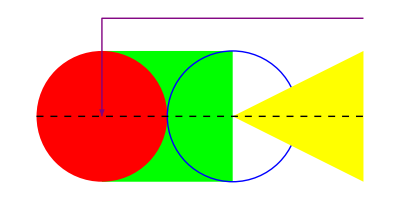
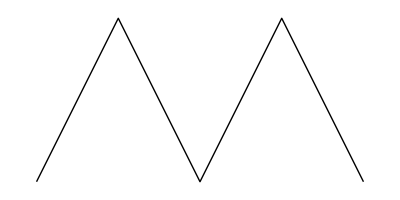
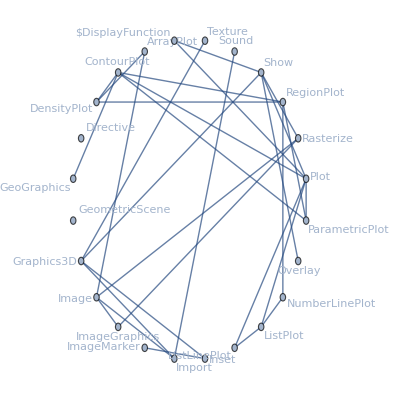
attributes | {Protected,ReadProtected}
character count | 8
common option values | {Epilog→{},Method→{{"AxesInFront"->False},{"FrameInFront"->False},{"GridLinesInFront"->True},{"TransparentPolygonMesh"->True}}}
date introduced | Day: Thu 23 Jun 1988
date last modified | Day: Wed 9 Jul 2014
dates modified | {Day: Tue 3 Sep 1996,Day: Tue 1 May 2007,Day: Tue 18 Nov 2008,Day: Mon 15 Nov 2010,Day: Wed 9 Jul 2014}
documentation basic examples | {{Use lines, polygons, circles, etc. to build up a graphics image:,Graphics[{Thick,Green,Rectangle[{0,-1},{2,1}],Red,Disk[],Blue,Circle[{2,0}],Yellow,Polygon[{{2,0},{4,1},{4,-1}}],Purple,Arrowheads[Large],Arrow[{{4,3/2},{0,3/2},{0,0}}],Black,Dashed,Line[{{-1,0},{4,0}}]}],-Graphics-}}
documentation example counts | {BasicExamples→2,Scope→13,GeneralizationsExtensions→0,Options→68,Applications→1,PropertiesRelations→5,PossibleIssues→0,InteractiveExamples→0,NeatExamples→2}
documentation example inputs | {BasicExamples→{{Graphics[{Thick,Green,Rectangle[{0,-1},{2,1}],Red,Disk[],Blue,Circle[{2,0}],Yellow,Polygon[{{2,0},{4,1},{4,-1}}],Purple,Arrowheads[Large],Arrow[{{4,3/2},{0,3/2},{0,0}}],Black,Dashed,Line[{{-1,0},{4,0}}]}]},{Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling→Axis],GraphPlot[Table[i→Mod[i^2,102],{i,0,102}]],ReliefPlot[Table[i+Sin[i^2+j^2],{i,-4,4,.03},{j,-4,4,.03}],ColorFunction→SunsetColors]}},Scope→{{Graphics[{Red,Disk[],Green,Rectangle[{0,0},{2,2}],Blue,Disk[{2,2}]}]},{Graphics[Polygon[{{0,0},{1,1},{0,1},{1,0}}]]},{v=Table[15{Cos[t],Sin[t]},{t,0,4Pi,4Pi/5}];,Graphics[GraphicsComplex[v,{Point[{1,2,3,4,5,6}],Green,Line[{1,2,3,4,5,6}]}]]},{Graphics[{Circle[],Inset[x^2+y^2==1,{0,0}]}]},{{Graphics[{Red,Disk[]}],Graphics[{Green,Disk[],Yellow,Opacity[.7],Disk[{0,1}]}],
Graphics[{Hue[2/3,1/2,1],Rectangle[]}]}},{{Graphics[{Blue,Arrow[{{0,0},{2,1}}]}],Graphics[{Thick,Blue,Line[{{0,0},{2,1}}]}],Graphics[{Dashed,Red,Arrow[{{0,0},{2,1}}]}],Graphics[{Thick,Dashed,Red,Line[{{0,0},{2,1}}]}]},{Graphics[{Pink,Rectangle[]}],Graphics[{EdgeForm[Thick],Pink,Rectangle[]}],Graphics[{EdgeForm[Dashed],Pink,Rectangle[]}],Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Pink,Rectangle[]}]}},{{Graphics[{Dashed,Red,Arrowheads[{-.1,.1}],Arrow[{{0,0},{2,1}}]}],Graphics[{Blue,PointSize[Large],Point[{{0,0},{1,1/2},{2,1}}]}]}},{Graphics[{Style[Disk[],Pink],Style[Rectangle[{2,-1},{4,1}],Blue]}]},{Graphics[{Pink,Disk[],{Blue,Disk[{1,0}]},Disk[{2,0}]}]},{Graphics[Rectangle[{0,4},{10,6}],Frame→True,PlotRange→{{0,10},{0,10}}]},{Graphics[Rectangle[Scaled[{0,.4}],Scaled[{1,.6}]],Frame→True,PlotRange→{{0,10},{0,10}}]},{Graphics[Rectangle[ImageScaled[{0,.4}],ImageScaled[{1,.6}]],Frame→True,PlotRange→{{0,10},{0,10}}]},{Graphics[Rectangle[Offset[{10,20},{0,0}],Offset[{-10,-20},{1,1}]],Frame→True]}},GeneralizationsExtensions→{},Options→{{Table[Graphics[{Inset[Graphics[Circle[],ImageSize→30,AlignmentPoint→{a,0}],Center]},ImageSize→70,Axes→True,Ticks→None],{a,{-1,0,1}}],Table[Graphics[{Inset[Graphics[Circle[],ImageSize→30,AlignmentPoint→{0,a}],Center]},ImageSize→70,Axes→True,Ticks→None],{a,{-1,0,1}}]},{Table[Graphics[Circle[],AspectRatio→1/k],{k,1,3}]},{Graphics[Circle[],Axes→True]},{Graphics[Circle[],Axes→{False,True}]},{Graphics[Circle[],Axes→True,AxesLabel→y]},{Graphics[Circle[],Axes→True,AxesLabel→{x,y}]},{Graphics[Circle[],Axes→True,AxesOrigin→Automatic]},{Graphics[Circle[],Axes→True,AxesOrigin→{0,-1}]},{Graphics[Circle[],Axes→True,AxesStyle→Directive[Orange,12]],Graphics[Circle[],Axes→True,AxesStyle→{Directive[Dashed,Red],Blue}]},{Graphics[Circle[],Background→LightBlue]},{{x,Graphics[Circle[],ImageSize→50,BaselinePosition→Center],y}},{Table[{x,Graphics[Circle[],BaselinePosition→Scaled[b],ImageSize→50]},{b,{0,0.5,1}}]},{{x,Graphics[Circle[],Axes→True,BaselinePosition→Axis],y},{x,Graphics[Circle[{0,1}],Axes→True,BaselinePosition→Axis],y}},{Graphics[{Circle[{0,0},1],Disk[{3,0},1]},BaseStyle→Blue]},{Graphics[{Circle[{0,0},1],Disk[{3,0},1]},BaseStyle→{Green,Thick,EdgeForm[Dashed]}]},{Graphics[{Pink,Disk[],Rectangle[{2,-1},{4,1}]},ContentSelectable→True]},{Graphics[{Pink,Disk[],Rectangle[{2,-1},{4,1}]},ContentSelectable→False]},{Graphics[{Pink,Disk[],Rectangle[{2,-1},{4,1}]},ContentSelectable→Automatic]},{Graphics[{Pink,Disk[]},Axes→True,Epilog→{Blue,Disk[{0,0},.4]}]},{Graphics[{Circle[],Text[Style[x^2+y^2==1,20]]}]},{Graphics[{Circle[],Text[Style[x^2+y^2==1,20]]},FormatType→StandardForm]},{Graphics[Circle[],Axes→True,AxesLabel→{Cos[θ],Sin[θ]},FormatType→StandardForm]},{Graphics[Circle[],Frame→True]},{Graphics[Circle[],Frame→{{True,True},{False,False}}]},{Graphics[Circle[],Frame→True,FrameLabel→{x,y}],Graphics[Circle[],Frame→True,FrameLabel→{{a,b},{c,d}}]},{Graphics[Circle[],Frame→True,FrameStyle→Directive[Thick,Gray]]},{Graphics[Circle[],Frame→True,FrameStyle→{{Thick,Directive[Thick,Dashed]},{Blue,Red}}]},{Graphics[Circle[],Frame→True,FrameTicks->None],Graphics[Circle[],Frame→True,FrameTicks→Automatic]},{Graphics[Circle[],Frame→True,FrameTicks→{{None,Automatic},{Automatic,None}}]},{Graphics[{},Frame→True,FrameTicksStyle→Directive[Orange,12]]},{Graphics[{},Frame→True,FrameTicks→All,FrameTicksStyle→{{Black,Blue},{Red,Green}}]},{Graphics[Circle[],GridLines→Automatic]},{Graphics[Circle[],Axes→True,GridLines→{{-1,1},{-1,1}}]},{Graphics[Circle[],Axes→True,GridLines→{{{-1,Orange},{-.5,Dotted},{.5,Dotted},{1,Orange}},{-1,{-.5,Dotted},{.5,Dotted},1}}]},{Graphics[Circle[],Axes→True,GridLines→Automatic,GridLinesStyle→Directive[Red,Dotted]]},{Framed[Graphics[Disk[]]]},{Framed[Graphics[Disk[],ImageMargins→20]]},{Framed[Graphics[Disk[],ImageMargins→{{5,10},{20,30}}]]},{Graphics[{Thickness[.3],Pink,Circle[]},ImagePadding→None,Frame→True,FrameLabel→{x,y}]},{Framed[Graphics[{Thickness[.3],Pink,Circle[]},ImagePadding→All,Frame→True,FrameLabel→{x,y}],FrameMargins→0]},{Framed[Graphics[{Thickness[.3],Pink,Circle[]},ImagePadding→40,Frame→True]]},{Framed[Graphics[{Thickness[.2],Pink,Circle[]},ImagePadding→{{40,10},{20,5}},Frame→True]]},{Table[Graphics[Circle[],ImageSize→s],{s,{Tiny,Small}}]},{{Graphics[Circle[],ImageSize→100],Graphics[Circle[{0,0},{1,2}],ImageSize→100]}},{{Graphics[Circle[],ImageSize→{100,100}],Graphics[Circle[{0,0},{1,2}],ImageSize→{100,100}]}},{Graphics[Circle[],Axes→True,AxesLabel→{x,y},LabelStyle→Orange]},{Graphics[{Red,Table[Disk[{i,i}],{i,-1,1}]},Axes→True,Method→{AxesInFront→False}],Graphics[{Red,Polygon[{{0.5,0},{.5,1},{-.5,1}}]},Frame→True,PlotRange→{{0,1},{0,1}}],Show[%, Method→{FrameInFront→False}],Graphics[{Green,PointSize[.6],Point[{0,0}]},GridLines→Automatic,Method→{GridLinesInFront→True}],Graphics[{Blue,Opacity[0.2],EdgeForm[None],
Polygon[{{{0,0},{0,1},{1,0}},{{1,1},{0,1},{1,0}}}]}],Show[%,Method→{TransparentPolygonMesh→True}]},{Graphics[Circle[],PlotLabel→x^2+y^2==1]},{Graphics[Circle[],PlotLabel→Style[Framed[x^2+y^2==1],16,Red,Background→Yellow]]},{Graphics[{Pink,Disk[{0,0},5]},Frame→True,PlotRange→All]},{Graphics[{Pink,Disk[]},PlotRange→{{-1,1},{0,1}},Frame→True],Graphics[{Pink,Disk[]},PlotRange→{{-1,1},{0,1}},PlotRangeClipping→True,Frame→True]},{Graphics[{Pink,Disk[{0,0},5]},Frame→True,PlotRange→4]},{Graphics[{Pink,Disk[{0,0},5]},Frame→True,PlotRange→4,PlotRangeClipping→False]},{Graphics[{Pink,Disk[{0,0},5]},Frame→True,PlotRange→4,PlotRangeClipping→True]},{Graphics[{Pink,Rectangle[]},PlotRangePadding→1,Frame→True]},{Graphics[{Pink,Rectangle[]},PlotRangePadding→Scaled[0.1],Frame→True]},{Graphics[{Pink,Rectangle[]},PlotRangePadding→{{0.5,1},{0.3,0.3}},Frame→True]},{Graphics[{Pink,Disk[]},Frame→True,FrameTicks→False,Background→LightBlue]},{Graphics[{Pink,Disk[]},Frame→True,FrameTicks→False,PlotRegion→{{0.25,0.75},{0.25,0.75}},Background→LightBlue]},{Graphics[{Pink,Disk[]},Frame→True,FrameTicks→False,ImagePadding→30,Background→LightBlue]},{bg=Graphics[Polygon[{{0,0},{1,0},{1,1},{0,1}},VertexColors→{Orange,Orange,White,White}],AspectRatio→Full];,Graphics[Circle[],Prolog→Inset[bg,Scaled[{0,0}],Scaled[{0,0}]]],Plot[Sin[x],{x,0,10},Prolog→Inset[bg,Scaled[{0,0}],Scaled[{0,0}],Scaled[{1,1}]]]},{Graphics[Circle[],Frame→True,FrameLabel→{None,y axis},RotateLabel→True]},{Graphics[Circle[],Frame→True,FrameLabel→{None,y axis},RotateLabel→False]},{Graphics[Circle[],Axes→True,Ticks→None]},{Graphics[Circle[],Axes→True,Ticks→Automatic]},{Graphics[Circle[{0,0},3],Ticks→{{1,2,3},{1,3}},Axes→True]},{Graphics[Circle[],Axes→True,TicksStyle→Directive[Red,Bold]]},{Graphics[Circle[],Axes→True,TicksStyle→{Directive[Red,Bold],Directive[Blue,12]}]}},Applications→{{pts=Table[{Cos[2n π/9],Sin[2 n π/9]},{n,0,8}];,Graphics[{Opacity[0.7],Red,Line[Tuples[pts,2]],Blue,PointSize[0.05],Point[pts]}]}},PropertiesRelations→{{Graphics[Disk[]],InputForm[%]},{makeDashed[ g_Graphics ]:=g/.l_Line:>{Dashed,l},makeDashed[-Graphics-]},{ParametricPlot[{(v+u) Cos[u],(v+u) Sin[u]},{u,0,4Pi},{v,0,5},Mesh→False],ContourPlot[y+Sin[x^2+3y],{x,-3,3},{y,-3,3},ColorFunction→Rainbow]},{CountryData[World,Shape],GraphData[DoubleStarSnark]},{First@Import[ExampleData/mathematica.pdf],Import[ExampleData/coneflower.jpg, Graphics]}},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{{Dynamic@Module[{hour,min,sec,ht,mt,st},Clock[];{hour,min,sec}=Take[DateList[],-3];ht=Pi/2-2Pi hour/12-2Pi min/720;mt=Pi/2-2Pi min/60;st=Pi/2-2Pi Floor[sec]/60;Graphics[{Arrowheads[0.1],Arrow[{{0,0},0.6{Cos[ht],Sin[ht]}}],Arrow[{{0,0},0.85{Cos[mt],Sin[mt]}}],Line[{{0,0},0.85{Cos[st],Sin[st]}}],PointSize[Medium],Table[Point[0.9{Cos[i],Sin[i]}],{i,0,2Pi,Pi/6}],Point[{0,0}],Circle[]}]]},{Graphics[Table[{Hue[t/20],Circle[{Cos[2Pi t/20],Sin[2Pi t/20]}]},{t,20}]]}}}
documentation example text | {BasicExamples→{{Use lines, polygons, circles, etc. to build up a graphics image:},{Use plot functions to automatically create Graphics from different types of data: }},Scope→{{Graphics primitives are drawn in the order in which they are given in Graphics:},{Polygons can fold over themselves:},{Vertices can be shared by using GraphicsComplex:},{Inset an expression in a graphic:},{Directives can specify color and opacity of faces:},{Colors, thickness, and dashing directives affect lines, arrows, and edges:},{Some primitives have special directives to specify various properties:},{Directives can be applied to individual objects using Style:},{Graphics directives remain in effect only until the end of the list that contains them:},{Use an ordinary coordinate system:},{Specify coordinates by fractions of the plot range:},{Specify coordinates by fractions of the whole image:},{Offset coordinates by printer's points:}},GeneralizationsExtensions→{},Options→{{Specify the coordinates within Inset to be aligned with the center of the enclosing graphic:},{Use numerical values for AspectRatio:},{Draw all the axes:},{Draw the y axis but not the x axis:},{Place a label for the y axis:},{Specify a label for each axis:},{Determine where the axes cross automatically:},{Specify the axes' origin explicitly:},{Specify the overall axes style, including the ticks and the tick labels:,Specify the style of each axis:},{Specify a background color:},{Align the center of a graphic with the baseline of the text:},{Specify the baseline of a graphic as a fraction of the height by using Scaled:},{Use the axis of a graphic as the baseline:},{Set the starting style:},{Set multiple starting styles:},{Allow the individual graphics objects to be selectable by a single click:},{No individual object is selectable; the whole graphic appears as one object:},{The first click selects the whole graphic, and subsequent ones select individual objects:},{Draw a disk above the graphic, including the axes:},{By default, expressions are displayed using TraditionalForm in graphics:},{Display expressions using StandardForm:},{Labels are also affected by FormatType setting:},{Draw a frame around the whole graphic:},{Draw a frame on the left and the right edges:},{Specify frame labels for the bottom and the left edges:,Specify labels for each edge:},{Specify the overall frame style:},{Specify the style of each frame edge:},{Put a frame, but no ticks:,Tick mark labels on the bottom and the left frame edges:},{Frame ticks on the bottom and the right edges:},{Specify frame tick and frame tick label style:},{Specify frame tick style for each edge:},{Put grids across a 2D graphic:},{Draw grid lines at specific positions:},{Specify the style of each grid:},{Specify the overall grid style:},{Allow no margins outside of ImageSize:},{Have 20-point margins on all sides:},{Leave different margins on each side:},{Leave no padding outside of the plot range:},{Leave enough padding for all objects and labels that are present:},{Specify the same padding for all sides in printer's points:},{Specify different padding on each side:},{Use predefined symbolic sizes:},{Use an explicit image width:},{Use an explicit image width and height:},{Specify the overall style of all the label-like elements:},{Force axes to be behind drawing primitives:,By default, frames draw in front of graphics primitives:,Force the frame to draw behind graphics primitives:,Force grid lines to be rendered in front of graphics primitives:,By default, polygon meshes double-paint their edges for efficiency reasons:,The behavior can be turned off using the TransparentPolygonMesh method option:},{Display a label on the top of the graphic in TraditionalForm:},{Use Style and other typesetting functions to modify how the label appears:},{Display all objects:},{Explicitly choose x and y ranges:,Force clipping at the PlotRange: },{PlotRange->s is equivalent to PlotRange->{{-s,s},{-s,s}}:},{Allow graphics objects to spread beyond PlotRange:},{Clip all graphics objects at PlotRange:},{Include 1 coordinate unit of padding on all sides:},{Include padding using Scaled coordinates: },{Specify different padding on each side:},{The contents of a graphic use the whole region:},{Limit the contents of the graphic to the middle half of the region in each direction:},{ImagePadding can also be used to add padding around a graphic:},{Define a simple graphic to use as a background:,Use it in multiple graphics:},{Specify that vertical frame labels should be rotated:},{Specify that vertical frame labels should not be rotated:},{Draw the axes but no tick marks:},{Place tick marks automatically:},{Draw tick marks at the specific positions:},{Specify the styles of the ticks and tick labels:},{Specify the styles of x and y axis ticks separately:}},Applications→{{Draw a complete graph with 9 vertices:}},PropertiesRelations→{{The StandardForm of Graphics is its rendered form:,The InputForm is the textual expression form:},{Graphics can be used as input to functions: },{Two-dimensional plot functions return Graphics:},{Several integrated data sources return Graphics:},{Many Import and Export formats support Graphics:}},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{{Display an analog clock with current system time:},{Digital dahlias:}}}
entity classes | {}
eponymous people | {}
equal-precedence symbols | Missing[NotApplicable]
external links | {Fast Introduction for Programmers: Graphics→http://www.wolfram.com/language/fast-introduction-for-programmers/graphics/}
frequencies of usage | {All→0.000574249,StackExchange→0.00205678,TypicalProductionCode→0.00141163,WolframAlphaCodebase→0.000162146,WolframDemonstrations→0.00266587,WolframDocumentation→0.00331944}
full version introduced | 1
full version last modified | 10
full versions modified | {3,6,7,8,10}
functionality areas | {BasicSymbols}
symbol background | Missing[NotAvailable]
keyboard shortcuts | Missing[NotAvailable]
link trails | {{guide/WolframRoot,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/EarthSciencesDataAndComputation,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/DateAndTime,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/DiscreteCalculus,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/DiscreteCalculus,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/EarthSciencesDataAndComputation,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/SolidGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/SolidGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/PlaneGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/PlaneGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/CloudFunctionsAndDeployment,guide/CloudExecutionMetadata,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/CreatingAnInstantAPI,guide/CloudExecutionMetadata,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/CreatingFormsAndApps,guide/CloudExecutionMetadata,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/DiscreteMathematics,guide/DiscreteCalculus,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/DiscreteMathematics,guide/DiscreteCalculus,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/Finance,guide/DateAndTime,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeographicData,guide/EarthSciencesDataAndComputation,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/InternetAndWebRelatedData,guide/CloudExecutionMetadata,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/MeshRegions,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/MeshRegions,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PeopleAndHistory,guide/DateAndTime,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PhysicsAndChemistryDataAndComputation,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PhysicsAndChemistryDataAndComputation,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/TimeSeries,guide/DateAndTime,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics}}
memberships | {}
name | Graphics
option names | {AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,ContentSelectable,CoordinatesToolOptions,DisplayFunction,Epilog,FormatType,Frame,FrameLabel,FrameStyle,FrameTicks,FrameTicksStyle,GridLines,GridLinesStyle,ImageMargins,ImagePadding,ImageSize,ImageSizeRaw,LabelStyle,Method,PlotLabel,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PreserveImageOptions,Prolog,RotateLabel,Ticks,TicksStyle}
options | {AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Method→Automatic,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}
plaintext usage | Graphics[primitives, options] represents a two-dimensional graphical image.
precedence ranks | Missing[NotApplicable]
ranks of usage | {All→72,StackExchange→47,TypicalProductionCode→66,WolframAlphaCodebase→111,WolframDemonstrations→38,WolframDocumentation→24}
related entities | Missing[NotAvailable]
related guide pages | {Plane Geometrypaclet:guide/PlaneGeometry,Symbolic Graphics Languagepaclet:guide/SymbolicGraphicsLanguage,Polygonspaclet:guide/Polygons,Polygonspaclet:guide/PolygonsNew,Polygons & Polyhedrapaclet:guide/PolygonsAndPolyhedra,Popular Functionspaclet:guide/PopularFunctions,Graphics & Visualizationpaclet:guide/GraphicsAndVisualization,WDF (Wolfram Data Framework)paclet:guide/WDFWolframDataFramework}
related symbols | {Plot,ListPlot,ListLinePlot,ParametricPlot,DensityPlot,ArrayPlot,RegionPlot,ContourPlot,Show,Graphics3D,Image,Import,GeometricScene,Sound}
relationship community graph | -Graphics-
relationship graph | -Graphics-
short notations | Missing[NotApplicable]
subject classifications | Missing[NotAvailable]
symbols linking to | {Directive,GeoGraphics,GeometricScene,Graphics3D,Image,ImageGraphics,ImageMarker,Inset,ListLinePlot,ListPlot,NumberLinePlot,Overlay,ParametricPlot,Plot,Rasterize,Sound,Texture,$DisplayFunction}
symbols using as attribute | {}
symbols using as option | {}
text strings | {Graphics[primitives,options] represents a two-dimensional graphical image.,Graphics is displayed in StandardForm as a graphical image. In InputForm, it is displayed as an explicit list of primitives.,The following graphics primitives can be used:139436543,The following graphics directives can be used:362437821,The following wrappers can be used at any level:,The following options can be given:,Nested lists of graphics constructs can be given. Directive specifications such as GrayLevel remain in effect only until the end of the list that contains them.415812662,Style[obj,opts] can be used to apply the options or directives opts to obj.59755747,The following Method options can be given:,The settings for BaseStyle are appended to the default style typically given by the "Graphics" style in the current stylesheet. The settings for AxesStyle, LabelStyle, etc. are appended to the default styles given for "GraphicsAxes", "GraphicsLabel", etc.,Graphics[] gives an empty graphic with the default image size.,Use lines, polygons, circles, etc. to build up a graphics image:,Use plot functions to automatically create Graphics from different types of data:,Graphics primitives are drawn in the order in which they are given in Graphics:,Polygons can fold over themselves:,Vertices can be shared by using GraphicsComplex:,Inset an expression in a graphic:,Directives can specify color and opacity of faces:,Colors, thickness, and dashing directives affect lines, arrows, and edges:,Some primitives have special directives to specify various properties:,Directives can be applied to individual objects using Style:,Graphics directives remain in effect only until the end of the list that contains them:,Use an ordinary coordinate system:,Specify coordinates by fractions of the plot range:,Specify coordinates by fractions of the whole image:,Offset coordinates by printer's points:,Specify the coordinates within Inset to be aligned with the center of the enclosing graphic:,Use numerical values for AspectRatio:,Draw all the axes:,Draw the y axis but not the x axis:,Place a label for the y axis:,Specify a label for each axis:,Determine where the axes cross automatically:,Specify the axes' origin explicitly:,Specify the overall axes style, including the ticks and the tick labels:,Specify the style of each axis:,Specify a background color:,Align the center of a graphic with the baseline of the text:,Specify the baseline of a graphic as a fraction of the height by using Scaled:,Use the axis of a graphic as the baseline:,Set the starting style:,Set multiple starting styles:,Allow the individual graphics objects to be selectable by a single click:,No individual object is selectable; the whole graphic appears as one object:,The first click selects the whole graphic, and subsequent ones select individual objects:,Draw a disk above the graphic, including the axes:,By default, expressions are displayed using TraditionalForm in graphics:,Display expressions using StandardForm:,Labels are also affected by FormatType setting:,Draw a frame around the whole graphic:,Draw a frame on the left and the right edges:,Specify frame labels for the bottom and the left edges:,Specify labels for each edge:,Specify the overall frame style:,Specify the style of each frame edge:,Put a frame, but no ticks:,Tick mark labels on the bottom and the left frame edges:,Frame ticks on the bottom and the right edges:,Specify frame tick and frame tick label style:,Specify frame tick style for each edge:,Put grids across a 2D graphic:,Draw grid lines at specific positions:,Specify the style of each grid:,Specify the overall grid style:,Allow no margins outside of ImageSize:,Have 20-point margins on all sides:,Leave different margins on each side:,Leave no padding outside of the plot range:,Leave enough padding for all objects and labels that are present:,Specify the same padding for all sides in printer's points:,Specify different padding on each side:,Use predefined symbolic sizes:,Use an explicit image width:,Use an explicit image width and height:,Specify the overall style of all the label-like elements:,Force axes to be behind drawing primitives:,By default, frames draw in front of graphics primitives:,Force the frame to draw behind graphics primitives:,Force grid lines to be rendered in front of graphics primitives:,By default, polygon meshes double-paint their edges for efficiency reasons:,The behavior can be turned off using the "TransparentPolygonMesh" method option:,Display a label on the top of the graphic in TraditionalForm:,Use Style and other typesetting functions to modify how the label appears:,Display all objects:,Explicitly choose x and y ranges:,Force clipping at the PlotRange:,PlotRange->s is equivalent to PlotRange->{{-s,s},{-s,s}}:,Allow graphics objects to spread beyond PlotRange:,Clip all graphics objects at PlotRange:,Include 1 coordinate unit of padding on all sides:,Include padding using Scaled coordinates:,Specify different padding on each side:,The contents of a graphic use the whole region:,Limit the contents of the graphic to the middle half of the region in each direction:,ImagePadding can also be used to add padding around a graphic:,Define a simple graphic to use as a background:,Use it in multiple graphics:,Specify that vertical frame labels should be rotated:,Specify that vertical frame labels should not be rotated:,Draw the axes but no tick marks:,Place tick marks automatically:,Draw tick marks at the specific positions:,Specify the styles of the ticks and tick labels:,Specify the styles of x and y axis ticks separately:,Draw a complete graph with 9 vertices:,The StandardForm of Graphics is its rendered form:,The InputForm is the textual expression form:,Graphics can be used as input to functions:,Two-dimensional plot functions return Graphics:,Several integrated data sources return Graphics:,Many Import and Export formats support Graphics:,Display an analog clock with current system time:,Digital dahlias:}
timeline | -Graphics-
timeline events | Interval[{Day: Thu 23 Jun 1988,Day: Wed 9 Jul 2014}]Graphics
translations | {Simplified Chinese→图形,Traditional Chinese→圖形,French→graphique,German→Graphik,Modern Greek→γραφικά,Japanese→グラフィックス,Korean→그래픽,Lithuanian→grafika,Polish→grafika,Portuguese→representação gráfica,Russian→графика,Spanish→gráfico,Ukrainian→графіка,Vietnamese→đồ họa}
typeset usage | Graphics[primitives,options] represents a two-dimensional graphical image. 
URL | http://reference.wolfram.com/language/ref/Graphics.html
version introduced | 1
version last modified | 10
versions modified | {3,6,7,8,10}
Wolfram documentation link | Graphicspaclet:ref/Graphics

```mathematica
Grid[MapThread[{#1,#2}&,{wlEntityProperties,graphicsWLProperties}],Frame->All]
```

```mathematica
simplePlot=Plot[2 x, {x,-2,2}];
```

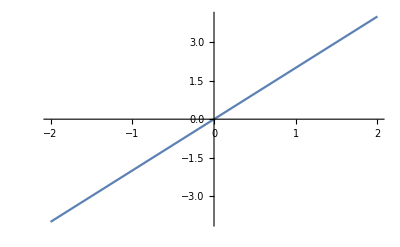

```mathematica
simplePlot
```

```mathematica
simplePlotFullForm = FullForm[simplePlot];
```

```mathematica
simplePlotInputForm = InputForm[simplePlot];
```

```mathematica
simplePlotFullForm
```

Graphics[List[List[List[List[],List[],Annotation[List[Directive[Opacity[1.],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]],Line[List[List[-2.,-4.],List[-1.99877,-3.99755],List[-1.99755,-3.99509],List[-1.99509,-3.99019],List[-1.99019,-3.98037],List[-1.98037,-3.96074],List[-1.96074,-3.92149],List[-1.92149,-3.84297],List[-1.83637,-3.67273],List[-1.75689,-3.51378],List[-1.67897,-3.35794],List[-1.59445,-3.18889],List[-1.51556,-3.03113],List[-1.43008,-2.86015],List[-1.34615,-2.6923],List[-1.26786,-2.53572],List[-1.18297,-2.36594],List[-1.10372,-2.20744],List[-1.02603,-2.05206],List[-0.941732,-1.88346],List[-0.863077,-1.72615],List[-0.777818,-1.55564],List[-0.694118,-1.38824],List[-0.616058,-1.23212],List[-0.531394,-1.06279],List[-0.452371,-0.904742],List[-0.366744,-0.733487],List[-0.282675,-0.56535],List[-0.204247,-0.408495],List[-0.119216,-0.238431],List[-0.0398244,-0.0796487],List[0.0380078,0.0760156],List[0.122444,0.244888],List[0.20124,0.40248],List[0.28664,0.57328],List[0.370481,0.740962],List[0.448681,0.897362],List[0.533485,1.06697],List[0.612649,1.2253],List[0.690254,1.38051],List[0.774463,1.54893],List[0.853031,1.70606],List[0.938204,1.87641],List[1.01774,2.03547],List[1.09571,2.19142],List[1.18029,2.36057],List[1.25922,2.51844],List[1.34476,2.68952],List[1.42874,2.85749],List[1.50708,3.01417],List[1.59203,3.18406],List[1.67133,3.34267],List[1.74908,3.49816],List[1.83343,3.66686],List[1.91214,3.82427],List[1.91351,3.82702],List[1.91488,3.82977],List[1.91763,3.83526],List[1.92312,3.84624],List[1.9341,3.86821],List[1.95607,3.91214],List[1.95744,3.91488],List[1.95881,3.91763],List[1.96156,3.92312],List[1.96705,3.9341],List[1.97803,3.95607],List[1.97941,3.95881],List[1.98078,3.96156],List[1.98353,3.96705],List[1.98902,3.97803],List[1.99039,3.98078],List[1.99176,3.98353],List[1.99451,3.98902],List[1.99588,3.99176],List[1.99725,3.99451],List[1.99863,3.99725],List[2.,4.]]]],"Charting`Private`Tag$277702#1"]]],List[]],List[Rule[DisplayFunction,Identity],Rule[Ticks,List[Automatic,Automatic]],Rule[AxesOrigin,List[0,0]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[DisplayFunction,Identity],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.05],Scaled[0.05]]]],Rule[PlotRangeClipping,True],Rule[ImagePadding,All],Rule[DisplayFunction,Identity],Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,List[True,True]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0,0]],RuleDelayed[DisplayFunction,Identity],Rule[Frame,List[List[False,False],List[False,False]]],Rule[FrameLabel,List[List[None,None],List[None,None]]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[Method,List[Rule["DefaultBoundaryStyle",Automatic],Rule["DefaultGraphicsInteraction",List[Rule["Version",1.2],Rule["TrackMousePosition",List[True,False]],Rule["Effects",List[Rule["Highlight",List[Rule["ratio",2]]],Rule["HighlightPoint",List[Rule["ratio",2]]],Rule["Droplines",List[Rule["freeformCursorMode",True],Rule["placement",List[Rule["x","All"],Rule["y","None"]]]]]]]]],Rule["DefaultMeshStyle",AbsolutePointSize[6]],Rule["ScalingFunctions",None],Rule["CoordinatesToolOptions",List[Rule["DisplayFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]],Rule["CopiedValueFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]]]]]],Rule[PlotRange,List[List[-2,2],List[-4.,4.]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.02],Scaled[0.02]]]],Rule[Ticks,List[Automatic,Automatic]]]]

```mathematica
simplePlotInputForm
```

Graphics[{{{{}, {}, Annotation[{Directive[Opacity[1.], RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
      Line[{{-1.999999918367347, -3.999999836734694}, {-1.9987731283177614, -3.997546256635523}, {-1.997546338268176, -3.995092676536352}, 
       {-1.995092758169005, -3.99018551633801}, {-1.9901855979706633, -3.9803711959413266}, {-1.9803712775739797, -3.9607425551479594}, 
       {-1.9607426367806124, -3.921485273561225}, {-1.9214853551938782, -3.8429707103877564}, {-1.8363665716581652, -3.6727331433163304}, 
       {-1.7568884657193913, -3.5137769314387826}, {-1.6789694047244954, -3.357938809448991}, {-1.594446123367355, -3.18889224673471}, 
       {-1.515563519607154, -3.031127039214308}, {-1.4300766954847084, -2.860153390969417}, {-1.3461489163061406, -2.6922978326122813}, 
       {-1.2678618147245122, -2.5357236294490244}, {-1.1829704927806393, -2.3659409855612785}, {-1.1037198484337056, -2.2074396968674113}, 
       {-1.0260282490306498, -2.0520564980612996}, {-0.9417324292653497, -1.8834648585306994}, {-0.8630772870969888, -1.7261545741939777}, 
       {-0.7778179245663834, -1.5556358491327669}, {-0.6941176069796561, -1.3882352139593122}, {-0.6160579669898679, -1.2321159339797358}, 
       {-0.5313941066378353, -1.0627882132756705}, {-0.4523709238827418, -0.9047418477654836}, {-0.3667435207654039, -0.7334870415308078}, 
       {-0.282675162591944, -0.565350325183888}, {-0.20424748201542325, -0.4084949640308465}, {-0.11921558107665804, -0.23843116215331608}, 
       {-0.03982435773483204, -0.07964871546966408}, {0.03800782066311598, 0.07601564132623197}, {0.12244421942330848, 0.24488843884661696}, 
       {0.20123994058656178, 0.40247988117312355}, {0.28663988211205954, 0.5732797642241191}, {0.3704807786936793, 0.7409615573873586}, 
       {0.44868099767835984, 0.8973619953567197}, {0.533485437025285, 1.06697087405057}, {0.6126491987752708, 1.2252983975505416}, 
       {0.6902539155813786, 1.3805078311627572}, {0.7744628527497309, 1.5489257054994618}, {0.853031112321144, 1.706062224642288}, 
       {0.9382035922548017, 1.8764071845096033}, {1.01773539459152, 2.03547078918304}, {1.0957081519843606, 2.191416303968721}, 
       {1.1802851297394454, 2.360570259478891}, {1.2592214298975912, 2.5184428597951825}, {1.3447619504179815, 2.689523900835963}, 
       {1.4287434259944938, 2.8574868519889876}, {1.507084223974067, 3.014168447948134}, {1.5920292423158844, 3.1840584846317688}, 
       {1.6713335830607627, 3.3426671661215255}, {1.749078878861763, 3.498157757723526}, {1.8334283950250079, 3.6668567900500157}, 
       {1.9121372335913134, 3.8242744671826268}, {1.913510088040939, 3.827020176081878}, {1.9148829424905645, 3.829765884981129}, 
       {1.9176286513898155, 3.835257302779631}, {1.9231200691883177, 3.8462401383766354}, {1.9341029047853218, 3.8682058095706435}, 
       {1.9560685759793301, 3.9121371519586603}, {1.9574414304289558, 3.9148828608579116}, {1.9588142848785812, 3.9176285697571624}, 
       {1.9615599937778323, 3.9231199875556646}, {1.9670514115763345, 3.934102823152669}, {1.9780342471733385, 3.956068494346677}, 
       {1.979407101622964, 3.958814203245928}, {1.9807799560725896, 3.961559912145179}, {1.9835256649718405, 3.967051329943681}, 
       {1.9890170827703426, 3.9780341655406852}, {1.9903899372199683, 3.9807798744399365}, {1.9917627916695937, 3.9835255833391874}, 
       {1.9945085005688448, 3.9890170011376895}, {1.9958813550184704, 3.991762710036941}, {1.9972542094680958, 3.9945084189361917}, 
       {1.9986270639177213, 3.9972541278354425}, {1.999999918367347, 3.999999836734694}}]}, "Charting`Private`Tag$277702#1"]}}, {}}, 
 {DisplayFunction -> Identity, Ticks -> {Automatic, Automatic}, AxesOrigin -> {0, 0}, 
  FrameTicks -> {{Automatic, Automatic}, {Automatic, Automatic}}, GridLines -> {None, None}, DisplayFunction -> Identity, 
  PlotRangePadding -> {{Scaled[0.02], Scaled[0.02]}, {Scaled[0.05], Scaled[0.05]}}, PlotRangeClipping -> True, ImagePadding -> All, 
  DisplayFunction -> Identity, AspectRatio -> GoldenRatio^(-1), Axes -> {True, True}, AxesLabel -> {None, None}, AxesOrigin -> {0, 0}, 
  DisplayFunction :> Identity, Frame -> {{False, False}, {False, False}}, FrameLabel -> {{None, None}, {None, None}}, 
  FrameTicks -> {{Automatic, Automatic}, {Automatic, Automatic}}, GridLines -> {None, None}, GridLinesStyle -> Directive[GrayLevel[0.5, 0.4]], 
  Method -> {"DefaultBoundaryStyle" -> Automatic, "DefaultGraphicsInteraction" -> {"Version" -> 1.2, "TrackMousePosition" -> {True, False}, 
      "Effects" -> {"Highlight" -> {"ratio" -> 2}, "HighlightPoint" -> {"ratio" -> 2}, 
        "Droplines" -> {"freeformCursorMode" -> True, "placement" -> {"x" -> "All", "y" -> "None"}}}}, 
    "DefaultMeshStyle" -> AbsolutePointSize[6], "ScalingFunctions" -> None, "CoordinatesToolOptions" -> 
     {"DisplayFunction" -> ({(Identity[#1] & )[#1[[1]]], (Identity[#1] & )[#1[[2]]]} & ), 
      "CopiedValueFunction" -> ({(Identity[#1] & )[#1[[1]]], (Identity[#1] & )[#1[[2]]]} & )}}, 
  PlotRange -> {{-2, 2}, {-3.999999836734694, 3.999999836734694}}, PlotRangeClipping -> True, 
  PlotRangePadding -> {{Scaled[0.02], Scaled[0.02]}, {Scaled[0.02], Scaled[0.02]}}, Ticks -> {Automatic, Automatic}}]

```mathematica
anotherPlot=-Graphics-;
```

```mathematica
anotherPlot//FullForm
```

Graphics[List[RGBColor[0,1,0],Thickness[Large],Rectangle[List[0,-1],List[2,1]],List[RGBColor[1,0,0],Disk[List[0,0]]],List[RGBColor[0,0,1],Circle[List[2,0]]],List[RGBColor[1,1,0],Polygon[List[List[2,0],List[4,1],List[4,-1]]]],List[RGBColor[0.5,0,0.5],Arrowheads[Large],Arrow[List[List[4,Rational[3,2]],List[0,Rational[3,2]],List[0,0]]],List[GrayLevel[0],Dashing[List[Small,Small]],Line[List[List[-1,0],List[4,0]]]]]]]

```mathematica
anotherPlot//InputForm
```

Graphics[{RGBColor[0, 1, 0], Thickness[Large], Rectangle[{0, -1}, {2, 1}], {RGBColor[1, 0, 0], Disk[{0, 0}]}, 
  {RGBColor[0, 0, 1], Circle[{2, 0}]}, {RGBColor[1, 1, 0], Polygon[{{2, 0}, {4, 1}, {4, -1}}]}, 
  {RGBColor[0.5, 0, 0.5], Arrowheads[Large], Arrow[{{4, 3/2}, {0, 3/2}, {0, 0}}], {GrayLevel[0], Dashing[{Small, Small}], 
    Line[{{-1, 0}, {4, 0}}]}}}]

```mathematica
graphicsPrimitiveSymbols=Select[functionalityAreasOfAllWLSymbols,Count[Last@#,"GraphicsPrimitiveSymbols"]>0&];
```

```mathematica
graphicsSymbols=graphicsPrimitiveSymbols⟦All,1⟧
```

{AASTriangle,ASATriangle,AffineHalfSpace,AffineSpace,Annulus,Arrow,BSplineCurve,Ball,BezierCurve,CapsuleShape,Circle,Circumsphere,Cone,ConicHullRegion,Cube,Cuboid,Cylinder,DiskSegment,Dodecahedron,Ellipsoid,EmptyRegion,FilledCurve,FullRegion,GraphicsComplex,HalfLine,HalfPlane,HalfSpace,Hexahedron,Hyperplane,Icosahedron,InfiniteLine,InfinitePlane,Insphere,JoinedCurve,Octahedron,Parallelepiped,Parallelogram,Polyhedron,Prism,Rectangle,RegularPolygon,SASTriangle,SSSTriangle,ShellRegion,Simplex,Sphere,SphericalShell,StadiumShape,Tetrahedron,Triangle,Tube}

```mathematica
Clear[ToGraphics]
ToGraphics[arg_]:=First@ToExpression@ToString[#,FormatType->StandardForm]&@arg
SetAttributes[ToGraphics,Listable]
```

```mathematica
graphicsPrimitiveSymbolsExamples =MapThread[
{#1,#2}&,
{graphicsSymbols, 
With[
{examples=Flatten/@EntityValue[graphicsSymbols,EntityProperty["WolframLanguageSymbol","DocumentationBasicExamples"]]},
examples
]
}
];
```

### A parenthesis - PrintDefinitions

PrintDefinitions, a function from the Wolfram Function repository, creates a notebook object for a WL symbol, containing the symbol documentation/definition content.

```mathematica
ResourceFunction["PrintDefinitions"]
```

```mathematica
PrintDefinitions@Graphics
```

yghv2_shm184FrontEndObject[LinkObject["yghv2_shm", 3, 1]]184System`Graphics

## Keywords

<Keyword1>

Keyword2

....

## Acknowledgment

Mentor: <Mentor first name and last name>

<text>

## References

<Ref1>

<Ref2>

...